3

解析函数的级数表示

高阶导数的Cauchy公式

∳_C (f(ξ)ⅆξ)/(ξ-z)^(n+1)=(2π ⅈ)/(n!)f^(n)(z)           其中：n=0 时退化为 Cauchy 公式

可用于计算一些定积分，其中 f(z) 必须在闭合回路围成的区域内解析。

这可理解为把被积函数的不解析部分归结到 1/(ξ-z)^(n+1) 中。

但是一般函数的积分如何计算？或者说，对一般的函数，能否将其非解析部分归结为 1/(ξ-z)^(n+1) ？

另一方面，我们已求得：∳_C ⅆz/(z-a)^n=2π ⅈ δ_(n,1)         如何利用这一性质计算积分？

——  若能将 f(z) 写成以下的级数形式，似乎不仅可以求出积分

f(z)   ⟹^(？？？？)  ∑_n c_n (z-a)^n

更重要的，还可以将函数在某点的“隐私”（奇异行为）给“人肉”、“曝光”出来，满足人们的窥视癖好。

因此，本章涉及的问题：

函数的级数表示：函数写成无穷项“幂”函数之和？f(z)   ⟹^(？条件？)  ∑_(n = ?) c_n (z-a)^n    —— “ 幂级数”？

求积分和无穷项的求和次序对调：∫[∑_n c_n (z-a)^n]ⅆz   ⟹^(？条件？)  ∑_n c_n ∫(z-a)^n ⅆz          交换和积次序

函数的奇异性（非解析特性）用 1/(z-a)^(n+1) 的形式来描述（正如高阶导数的Cauchy公式）

所有这些问题，都指向一个概念：级数。我们将会遇见复变函数的第三个大Ⅴ ：Weierstrass（Cauchy、Riemann）

我们遇见的前两个大 V 是谁？（Cauchy、Riemann）

## 3.1 复变函数项级数

为讨论复变函数的幂函数形式的级数表示：∑_n c_n (z-a)^n，先讨论一般函数项级数。

许多概念仅为实变函数的一点拓展。

### 复变函数级数的敛散性

复变函数级数：简而言之，无穷级数，每一项都是一个复变函数，无穷项之和

(∑_(k=0))^∞ w_k(z)=w_0(z)+w_1(z)+w_2(z)+...

收敛：

部分和：S_n(z)=(∑_(k=0))^n w_k(z)         前 n 项之和，有限项求和一定收敛（也不必引入收敛的概念）

如果极限lim_(n→ ∞) S_n(z) =S(z) 对某一点 z 存在，则称

复变函数级数在 z 点收敛。S(z)称为复变函数级数在 z 点的和。

因为 w_k(z)=u_k(x,y)+ⅈ v_k(x,y)，故复变函数级数可视为两个有序二元实变函数级数，

复函数级数收敛     ⟺^等价     两二元实变函数级数收敛。

∑_k w_k(z) 收敛            (⟺^等价)^      ∑_k u_k(x,y)  和 ∑_k v_k(x,y)  都收敛

收敛的必要条件：  lim_(k→∞) w_k(z)=0，         —— 这一点与实变函数相同

容易理解：因为若 k→∞ 时 w_k(z) 不趋于 0，则级数的和将总是在做有限幅度的变化，自然也就不收敛。

证明： lim_(k→∞) w_k(z)= lim_(k→∞) [S_k(z)-S_(k-1)(z)]  ⟹^(级数收敛、极限存在) lim_(k→∞) S_k(z)-lim_(k→∞) S_(k-1)(z)=S(z)-S(z)=0

收敛的充要条件—— Cauchy 判据      （实际上这个判据与实变函数级数也相同）

∀ε>0，∃N(ε,z)，使得当  n>N(ε,z) 时，对任意自然数 p，均有

|S_(n+p)(z)-S_n(z)|=|(∑_(k=1))^p w_(n+k)(z)|<ε

理解：在 n>N 处连续取任意有限个项，这些项的和可以小于任意小。

收敛的必要条件：lim_(k→∞) w_k(z)=0  对应于 p=1。

### 绝对收敛

定义： (∑_(k=0))^∞|(w^)_k(z)|  在 z点收敛，则称函数级数 (∑_(k=0))^∞w_k(z) 在 z 点绝对收敛。

若级数本身收敛，各项加绝对值之后的级数不收敛，则称条件收敛。

若级数绝对收敛，则该级数一定收敛，反之不然。  ——  你能否证明这一性质？（Cauchy 判据）

绝对收敛的判别法 （与实变函数相同，因为加绝对值之后就变为实变函数了）

比值法：

lim_(n→∞) (|w_(n+1)(z)|)/(|w_n(z)|)=q    Piecewise[{{q<1,, 绝对收敛}, {q>1,, 发散}, {q=1，, 不确定}}]

OverBar[lim_(n→∞)](|w_(n+1)(z)|)/(|w_n(z)|)<1       绝对收敛   （用于极限不存在情况）

UnderBar[lim]_(n→∞)(|w_(n+1)(z)|)/(|w_n(z)|)>1       发散

根式法

lim_(n→∞) (|w_n(z)|)^(1/n)=q    Piecewise[{{q<1,, 收敛}, {q>1,, 发散}, {q=1，, 不确定}}]

OverBar[lim_(n→∞)](|w_n(z)|)^(1/n)=q     Piecewise[{{q<1,, 收敛}, {q>1,, 发散}, {q=1, 不确定}}]

高斯法，当比值法遭遇 q=1 时常用，当 n 足够大时，把 w_n/(w_(n+1)) 写成如下形式

w_n/(w_(n+1))=1+μ/n+o(1/n^λ),  λ>1， 则    Piecewise[{{Re μ>1, 收敛}, {Re μ ≤ 1, 发散}}]

注意区别：高斯法中判别   w_n/(w_(n+1)) ，比值法中判别  |(w_(n+1)(z))/(w_n(z))|

比较法

∑_n |v_n|收敛且  |u_n|≤ |v_n|, 则 ∑_n |u_n| 收敛

∑_n |v_n|发散且  |u_n|≥ |v_n|, 则 ∑_n |u_n| 发散

Dirichlet 判别法     证明见后

若 a_k 随 k 增大单调变化且趋于 0， (∑_(k=1))^n b_k  对任意 n 有界，则级数 (∑_(k=1))^∞ a_k b_k  收敛

例：(∑_(k=1))^∞(-1)^k/k,    (∑_(k=1))^∞z^k/(√k) 在圆心于原点的单位圆圆周上除 z=1点之外收敛

绝对收敛的性质

级数各项次序可任意调换，级数仍绝对收敛且级数和不变。

简而言之：绝对收敛的级数满足加法交换律（条件收敛的级数不一定满足加法交换律）

非绝对收敛级数的求和不一定能任意改变次序

I=1 - 1/2 + 1/3 - 1/4+1/5-1/6+...  =(∑_(k=1))^∞(-1)^k/k  非绝对收敛，只是条件收敛（满足 Dirichlet 判别法的条件）

以下推导是错误的，因为只有绝对收敛才可以改变求和顺序（“关门，放加法交换律？”）

I= [1+(1/2-2×1/2)+1/3+(1/4-2×1/4)+1/5+(1/6-2×1/6)+....]    接着交换次序
= (1+1/2+1/3+1/4+...)-2×(1/2+1/4+1/6+....)
=(1+1/2+1/3+1/4+...)-(1+1/2+1/3+1/4+....)=0   （实际上 I 显然大于 0）

实际上   I=ln 2

```mathematica
Sum[(-1)^(n-1)/n,{n,1,∞}]
```

Log[2]

可逐项相乘，下式右边仍为绝对收敛级数（乘法分配率与交换律？）

(∑_k u_k)(∑_l v_l)=∑_k ∑_l u_k v_l           绝对收敛是此式成立的充分条件

例题，类似于实函数级数

试证：当 |z|<1,       (∑_(k=0))^∞z^k=1/(1-z)

证明：利用比值法  lim__(k→∞)|z^k/z^(k-1)|=|z|<1 时，级数绝对收敛

S_n(z)=1+z+z^2+...+z^n,    z S_n(z)=z+z^2+...+z^(n+1)

二者相减：(1-z)S_n(z)=1+z+z^2+...+z^n-(z+z^2+...+z^(n+1))=1-z^(n+1)

两边取极限：lim_(n→∞) (1-z)S_n(z)=lim_(n→∞) (1-z^(n+1))

(1-z)lim_(n→∞) S_n(z)=1-lim_(n→∞) z^(n+1)=1,     S(z)=1/(1-z)

### 一致收敛

一致：显然应是对某区域或某条曲线而言，不是对一点而言。不同于前述的收敛与绝对收敛（可以对点而言）。

一致收敛概念在积分中有重要应用，正如一致连续概念。在实分析中，就有一致收敛的概念。

定义：级数 ((∑_)_(k=0))^∞w_k(z) 的每一项在区域 D或曲线 L上有定义

∀ε>0, 存在与 z 无关的 N(ε)，使得当 n>N(ε) 时，对任意 z∈D 或  z ∈L，均有

|S(z)-S_n(z)|<ε,     其中：S_n(z)=∑_(k=0)^n w_k(z)

则称级数在区域D或曲线L上一致收敛于 S(z)。

一致收敛的充要条件（Cauchy 判据）： 与收敛的概念之差别，仅在于 N 与 z 无关

∀ ε > 0， ∃ N(ε)，使得当 n > N(ε)  时，对任意 z∈D 或  z ∈L，对任意自然数 p，均有

|S_(n+p)(z)-S_n(z)|=| ∑_(k=1)^p w_(n+k)(z)|<ε

简而言之，就是对任意 z∈D 或 z∈L，存在与 z 无关的 N(ε)，

使得在 N(ε) 之后的任意连续的项之和的模小于 ε，如下图

注意区别绝对收敛和一致收敛，前者可以对点 z 定义，后者仅对区域或曲线而定义；

一致收敛与收敛的区别：找到一个对 z 在区域 D 或曲线 L 上变化时的最大 N(ε)。

一致收敛的充要条件：（Cauchy 判据）

∀ （任意） ε > 0， ∃（一个） N(ε)，使得当 n > N(ε) 时（对任意的 n > N），对任意 z∈D 或  z ∈L，对任意自然数 p，均有

|S_(n+p)(z)-S_n(z)|=| ∑_(k=1)^p w_(n+k)(z)|<ε         （N 之后的任意个连续项之和的模小于 ε）

一如特朗普那般任性，容易受弹劾。暗示要证明非一致收敛常用反证法。

例题：绝对收敛但不是一致收敛例

级数∑_k (z^(k-1)-z^k)在区域|z|<1

解：由比值判别法

|(w_(k+1)(z))/(w_k(z))|=|z|<1，⟹   绝对收敛

试试看能不能证明一致收敛。

用  ε-N 判别：∀ε>0, 需要导出存在 N，使得对任意  n>N ，| ∑ _(k=1)^p w_(n+k)(z)|<ε 成立

也就是应该导出使 | ∑ _(k=1)^p w_(n+k)(z)|<ε 成立的充分条件是 n>N ，且 N 与 z 无关。

任意 p 项之和，w_k=z^(k-1)-z^k

| ∑_(k=1)^p w_(n+k)(z)|<ε    ⟺^   |z^n| |1-z^p|<ε，在区域|z|<1有 |1-z^p|<2

⟸      2|z^n|<ε      ⟸      n>(ln ε/2)/(ln |z|)=N(ε,z)      找到 N ，因此级数是收敛的。

注：A  ⟸  B  理解为：B 是 A 成立的充分条件

但，若要证明级数一致收敛，则需要找一个与 z 无关的 N，

为此，应该对 z 在区域 |z|<1 内 ，看看能否找一个最大的 N 值。

由于我们求得的 N(ε,z)=(ln ε/2)/(ln|z|),  对 |z|<1区域，随着 |z| 靠近 1，N(ε,z) 越来越大，故对 |z|<1区域，

N(ε,z) 似乎没有最大值，应该不是一致收敛。然而是否一定找不到 N(ε,z)的最大值，则需要证明。

证：证明级数非一致收敛，鉴于其“特别任性”（见下），常利用反证法。

假设该级数一致收敛，那么对任意  ε>0，均可找到一个与 z 无关的 N(ε)，使得对任意 n>N ，

对任意 自然数 p 与满足 |z|<1的任意 的 z，均有：|∑_(k=1)^p w_(n+k)(z)|<ε。

下用反证法证明，对 p=1 和某些满足 |z|<1的复数值，就不满足上面的 (1.EquationNumbered)式。

对 n=N+1, p=1，取 z_0=-1+10^-M（模足够靠近 1 ）。显然对任意正整数 M，z_0 均满足 |z_0|<1。

p=1时，判据 (1.EquationNumbered)式退化为：注意 w_k=z^(k-1)-z^k

(|∑_(k=1)^p w_(n+k)(z_0)|)_(p=1)=|w_(n+1)|=|w_(N+2)|=|z_0^(N+1)-z_0^(N+2)|=((1-10^-M)_(⏟_(|z_0|)))^(N+1)|(2-10^-M)_(⏟_(1-z_0))|>(1-10^-M)^(N+1)

因为找到的 N 与 z 无关，M 变化时，虽然 z 变，但 N 不变，

因此对那个找到的与 z 无关的 N(ε)，我们可以取足够大的 M，

使得 (|∑_(k=1)^p w_(n+k)(z)|)_({p=1
n=N+1
z=z_0)>(1-10^-M)^(N+1)>ε，这就与(1.EquationNumbered)式相矛盾。

故找不到与 z 无关的 N。该级数不可能是一致收敛的。

理解（注意，这里的理解并非数学证明）：前面已求得 N(ε,z)=(ln ε/2)/(ln |z|) 与 z 有关，

接着应该在区域  |z|<1内找到一个最大的 N。

显然，在区域  |z|<1内，(ln ε/2)/(ln |z|)无最大值（因为|z| 可以无限接近于 1）。

若在 |z|<1/2 区域， N(ε,z) =(ln ε/2)/(ln|z|) 在此区域可取最大值,

对应于  |z|=1/2       ⟹    (ln  ε/2)/(ln 1/2)= N(ε) 与 z 无关。

例题：一致收敛但不是绝对收敛例：

级数(∑_(k=1))^∞(-1)^k z^k/k在曲线L：Piecewise[{{0≤x≤1, }, {y=0, }}]上 （实轴上的一段）

比值法：lim_(n→∞) | (w_(n+1))/w_n|=|z|   ⟹ 在 |z|<1区域绝对收敛。

在 z=1点，|w_n|=1/n,  发散， 或应用高斯法

(|w_n|)/(|w_(n+1)|)=1+1/n=1+μ/n+o(1/n^λ),    λ>1,   Re μ=1  发散

原级数在 L 上并非绝对收敛级数（并非在 L 上处处绝对收敛）。

下证明它在 L 上是一致收敛的。

∀ε>0, 要找一个与 z 无关的 N(ε)，使得

当 n >N 时，对任意自然数 p，I=|(∑_(k=1))^p w_(n+k)(z)|<ε。

现必须从 I<ε 出发，导出 I<ε 成立的充分条件是  n>N(ε)。在 L 上

I=|z^(n+1)/(n+1)-z^(n+2)/(n+2)+z^(n+3)/(n+3)-z^(n+4)/(n+4)+... |                         
=(|z|)^(n+1)/(n+1)[1-(n+1)/(n+2)z+(n+1)/(n+3)z^2-(n+1)/(n+4)z^3+...]

下面导出：只要 z 在曲线 L：{0≤x≤1
y=0 上， I<ε 的充分条件是 n >N（N 与 z 无关）

I 表达式的方括号内，当 z 在 L 上时，第一项大于第二项，第三项大于第四项...，因此，

若总项数 p 为偶数，必大于 0，即任意偶数项之和大于 0（对 z 在 L 上）

若总项数 p 为奇数，因偶数项之和 >0，最后一项（奇数项）也>0，总和仍>0

故：中括号内各项之和总大于 0，只要 p 是自然数。

又：对 z 在 L 上，每一项的绝对值都比后一项大并且是正负交替的，

故：前 奇数项之和<1，前偶数项中，因为最后一项小于0，故前偶数项也小于 1，

因此，中括号内各项之和大于 0  小于 1，故  I<(|z|)^(n+1)/(n+1)<1/(n+1)

I< ε   ⟸  1/(n+1)<ε    ⟸   n>ln 1/ε-1,   取 N=ln 1/ε  即可，

N 与 z 无关（只要 z 在曲线L：Piecewise[{{0≤x≤1, }, {y=0, }}]上）

实际上 ，对 |z|≤1 且  z≠ -1 ， (∑_(k=1))^∞(-1)^k z^k/k=- ln(1+z),

```mathematica
Sum[(-1)^k z^k/k,{k,1,∞}]
```

-Log[1+z]

实际上，该复数级数在 |z|≤ 1-δ 闭区域一致收敛（δ>0，δ 可任意小）—— 内闭一致收敛

下面是基本思路，详细的证明可见 Dirichlet 判别法的证明。

借助 \[MathematicaIcon] Mathematica 初步判断在闭区域 |z|≤1-δ ，这个级数一致收敛（这里的判断并非证明）

对 |z|≤ 1-δ （小量 δ>0），Cauchy一致收敛判据中的任意连续的 p 项和要满足

|S_(n+p)(z)-S_n(z)|=| ∑_(k=1)^p w_(n+k)(z)|<ε     从 n+1到 n+p 的 p 项之和的模小于 ε

可用 \[MathematicaIcon] Mathematica 计算     T_p(z,n)= (n+1) [S_(n+p)(z)-S_n(z)],

并验证 对任意自然数 p， |T_p(z,n)| <M （有界）

从而   |S_(n+p)(z)-S_n(z)|=(|T_p(z,n)|)/(n+1)<M/(n+1) <ε    ⟹  N=M/ε

下图为 T_p(z,n) 在 z=ⅇ^(ⅈ 127°), n=100, p 从 1 到 50 的值，箭号表示从 T_p 到 T_(p+1)，红色点为 T_1

作图程序：code03.01 uniformconvergence.nb

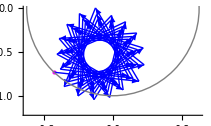

当然，以上并非证明，但给我们一个图像：

Cauchy 判据中的 |S_(n+p)(z)-S_n(z)| 乘以 (n+1) 在“兜圈”（有界），不妨换个辐角 arg z 试试

这种“兜圈”形式的级数之敛散性的证明将在下一节讨论（Dirichlet 判别法）。

内闭一致收敛：在开区域 D 内的任意闭区域（不包含 D_的边界）一致收敛，称在开区域 D 上 内闭一致收敛。

闭区域解析：从闭区域扩展到开区域。即：能找到一个包含闭区域的开区域，在这个开区域内，函数解析。

内闭一致收敛：从开区域塌缩到闭区域。在开区域内的任何一个闭区域上一致收敛。

注意其定义方式貌似不同。但若将闭区域解析理解为某开区域的“内闭区域解析”，两者就有相似之处。

在开区域 D 内一致收敛则一定在 D 内闭一致收敛（存在 N 的最大值），反之不然。

例： 级数 ∑_k z^k 在 |z|<1 区域绝对收敛、内闭一致收敛，但在开区域 |z|<1 并不是一致收敛。

一致收敛实用判别法：（高斯判据“略输文采”，Cauchy判据“稍逊风骚”，Dirichlet判别法“只识弯弓射大雕”，数风流判据还看今朝）

若常数项（每一项均为常数）级数 ∑_k m_k每一项均大于 0 且级数收敛，并且，若对任意 k，

在区域 D 或曲线 L 上，恒有 |w_k(z)|≤m_k，则级数 ∑_k w_k(z) 在 D 或 L 上绝对且一致收敛。

级数 ∑_k m_k 常被称为  ∑_k w_k(z) 的优级数

证：因为正项级数 ∑_k m_k收敛，  ∀ ε>0, ∃ N （与 z 无关）,  使得 n>N 时对任意 p，有 | ∑_(k=1)^p m_(n+k)|<ε

⟹   | ∑_(k=1)^p w_(n+k)(z)| ≤  ∑_(k=1)^p |w_(n+k)(z)|< | ∑_(k=1)^p m_(n+k)|<ε

⟹   故 级数   ∑_k |w_k(z)|  在 D 或 L 上一致收敛，即： ∑_k w_k(z) 绝对且一致收敛

在区域 D 或曲线 L 上：级数 ∑_k w_k(z) 一致收敛，函数|v(z)|<M （常数）， 则级数 ∑_k v(z)w_k(z) 在 D 或 L 上一致收敛。

证：因为级数 ∑_k w_k(z) 一致收敛，设它收敛于 S(z)，故  ∀ ε/M>0, ∃ N （与 z 无关）,

使得 n>N 时，有 |S(z)- ∑_(k=1)^n w_k(z)|<ε/M ,  （收敛的定义）

又   |v(z)S(z)- ∑_(k=1)^n v(z)w_k(z)|=|v(z)| |S(z)- ∑_(k=1)^n w_k(z)|< M|S(z)- ∑_(k=1)^n w_k(z)|

⟹    |v(z)S(z)- ∑_(k=1)^n v(z)w_k(z)|< ε    ⟹     级数 ∑_k v(z)w_k(z) 在 D 或 L 上一致收敛。

若级数  ∑_k w_k(z) 在D 或 L 上绝对且一致收敛且v(z)有界， 则级数 ∑_k v(z)w_k(z) 在 D 或 L 上绝对且一致收敛。

所以，

要判断一致收敛：

(1) 找优级数 ；  (2) 把级数的每一项写成一个一致收敛的级数与一个有界函数之积。

级数 ∑_k z^k 在 |z|<1 区域内找不到优级数，但在 r<1 的任何闭区域 |z|≤ r，则可找到优级数： ∑_k q^k,  r<q<1，故它是内闭一致收敛。

一致收敛级数的性质

连续性（逐项求极限）

若级数  ∑_k w_k(z) 在区域 D内满足：a. 每一项连续；b. 一致收敛，则其和函数

S(z)=((∑_)_(k=0))^∞w_k(z)  在 D 内连续，即：

lim__(z→z_0)S(z)=Ŝ(z_0)            此式左边为：lim__(z→z_0)S(z)

此式右边=((∑_)_(k=0))^∞w_k(z_0) =((∑_)_(k=0))^∞lim__(z→z_0)w_k(z)

故：lim__(z→z_0)S(z)= ((∑_)_(k=0))^∞lim__(z→z_0)w_k(z)        （此蓝色等式可理解为逐项求极限）

证明： 要证明方框内的等式，须证明对任意 z_0∈D，当 z→z_0时， S(z)→S(z_0)

即：应证明  ∀ε>0, ∃δ, 使得当 |z-z_0|<δ 时，I=|S(z)-S(z_0)| <ε。

论证步骤：从|S(z)-S(z_0)| <ε    ⟸   |z-z_0|<δ(ε)    （ 这里的 ⟸ 表示右边是左边的充分条件）

I=|S(z)-S(z_0)|=|S(z)-S_n(z)+S_n(z)-S_n(z_0)+S_n(z_0)-S(z_0)|

I<|S(z)-S_n(z)|+|S_n(z)-S_n(z_0)|+|S_n(z_0)-S(z_0)|

因为一致收敛，故 ∀ε/3>0, ∃与 z 无关的 N(ε), 使得当 n>N(ε) 时

|S(z)-S_n(z)|<ε/3      （因为级数一致收敛，故对 z 与 z_0，N 相同）

|S(z_0)-S_n(z_0)|<ε/3      （因为一致收敛，不同的 z 可共享一个相同的 N）

每一项连续，有限项之和必连续，对 ε/3,  ∃ δ, 使得

|z-z_0|<δ 时，|S_n(z)-S_n(z_0)|<ε/3

综上， ∀ε>0，∃ δ，使得 |z-z_0|<δ 时

I=|S(z)-S(z_0)|<ε     ⟹    S(z) 连续（连续的极限定义）

一致收敛是和函数连续的充分条件（但不是必要条件）。

若非一致收敛，则不一定能保证和函数的连续性。

反例：级数     (∑_(k=1))^∞[x^(k-1)-x^k ]

在 |x|<1收敛，在 x=1也收敛

在  0≤ x≤ 1 收敛，但并非一致收敛

S(x)=1/(1-x)-x/(1-x)=1,    0≤ x< 1    （绝对收敛，故可以这样写成两个级数）

S(1)=0,        lim_(x→1) S(x)=1 ≠ S(1)     级数 S(x) 在 x=1不连续

反例：级数     (∑_(k=0))^∞[z^(k+1)/(k+1)-(2 z^(2k+3))/(2k+3)]

在直线段 L：Piecewise[{{y=0, }, {-1<x≤1, }}]收敛     因为   |x|<1 时，比值法判别收敛，x=1时，w_k=1/((k+1)(2k+3))收敛

实际上它至少在圆心于原点的右半单位圆 D̄ 收敛。

可以证明，它在 L 上不是一致收敛，

S(z)=2z-ln[z+1]

lim_(z→1) S(z)=2-ln2     而     S(1)=2-ln4

lim_(z→1) S(z) ≠ S(1)       尽管在 D̄ 上收敛

```mathematica
z0=1-δ 0;
Sum[z^(k+1)/(k+1)-2 z^(2k+3)/(2k+3),{k,0,∞}]//FullSimplify
t1=Limit[%,z->z0]
t2=Sum[(z0^(n+1)/(n+1)-2 z0^(2n+3)/(2n+3)),{n,0,∞}]//FullSimplify
```

2 z-Log[1+z]

2-Log[2]

2-Log[4]

是否绝对收敛影响加法交换律在无穷级数中的应用，是否一致收敛影响连续函数之和依然连续在无穷级数中的应用。

换句话说：若不是绝对收敛，“加法交换律”在无穷级数中未必成立，若不是一致收敛，“连续函数之和依然连续”在级数中未必成立。

实际上，是否绝对收敛，还影响乘法分配律在无穷级数中的应用，记得：(∑_k u_k)(∑_l v_l)=∑_k ∑_l u_k v_l 成立的充分条件是绝对收敛。

逐项求积

若级数  ∑_k w_k(z) 在曲线 L_ 上满足：a. 每一项连续；b. 一致收敛，则：

∫_L [((∑_)_(k=0))^∞w_k(z)]ⅆz =((∑_)_(k=0))^∞ ∫_L w_k(z)ⅆz,   求积与求和可以交换次序，逐项求积

“曾记否，到中流击水，浪遏飞舟！”， 用现在的话就是：不忘初心，牢记使命。

∫[∑_n c_n (z-a)^n]ⅆz   ⟹^(？条件？)  ∑_n c_n ∫(z-a)^n ⅆz        交换和积次序

证明： 在 L_上一致收敛，故在 L_上“和函数” S(z) 连续，可积。

对有限项：∫_L S_n(z)ⅆz=∫_L [((∑_)_(k=0))^n w_k(z)]ⅆz=(∑_(k=0))^n∫_L w_k(z)ⅆz

#### 思考：下面的证明错在哪里？（好像证明与一致收敛没什么关系）

(1.EquationNumbered)式两边同取极限：lim_(n→∞) ∫_L [((∑_)_(k=0))^n w_k(z)]ⅆz=lim_(n→∞) ((∑_)_(k=0))^n∫_L w_k(z)ⅆz

左=lim_(n→∞) ∫_L [((∑_)_(k=0))^n w_k(z)]ⅆz=∫_L lim_(n→∞) ((∑_)_(k=0))^n w_k(z)ⅆz=∫_L ((∑_)_(k=0))^∞w_k(z)ⅆz      （求极限与求积可对调乎？一致收敛方可）

右=((∑_)_(k=0))^∞∫_L w_k(z)ⅆz     ⟹    左=右，得：∫_L ((∑_)_(k=0))^∞w_k(z)ⅆz=((∑_)_(k=0))^∞∫_L w_k(z)ⅆz

#### 正确的证明：

正确的证明：因为一致收敛，∀ε>0, ∃与 z 无关的 N(ε),

当 n>N 时，对任意 z∈L,  均有|S_n(z)-S(z)|<ε

(1.EquationNumbered)左=∫_L S_n(z)ⅆz=∫_L S(z)ⅆz+∫_L [S_n(z)-S(z)]ⅆz=∫_L S(z)ⅆz+I

I=∫_L [S_n(z)-S(z)]ⅆz,   因为一致收敛，∃与 z 无关的 N(ε)，

故无论 z 在积分路线 L 上如何变，均有 n >N 时， |S_n(z)-S(z)|<ε    ⟹   |I|<ε l     或     lim_(n→∞) I=0

lim_(n→∞) 左=lim_(n→∞) 右     ⟹  ∫_L [((∑_)_(k=0))^∞w_k(z)]ⅆz=((∑_)_(k=0))^∞∫_L w_k(z)ⅆz

若加上 w_k(z) 在 D 内解析，则级数 ((∑_)_(k=0))^∞∫_z_0^z w_k(z)ⅆz 也一致收敛。（试证之）

换言之：一致收敛级数逐项求积后得到的“原函数”级数，仍一致收敛。（要得到原函数，自然要求w_k(z)解析。）

提示：n>N 时任意 p 项和的模：|((∑_)_(k=1))^p∫_z_0^z w_(k+n)(z)ⅆz| =|∫_z_0^z ((∑_)_(k=1))^p w_(k+n)(z)ⅆz|≤∫_z_0^z (|((∑_)_(k=1))^p w_(k+n)(z)|)_(⏟_一致收敛柯西判据)|ⅆz|≤ε∫_z_0^z |ⅆz|=l ε

逐项求导（Weierstrass 定理）

若级数  ∑_k w_k(z) 在区域 D_（边界为 C，如图）内满足：a. 每一项解析；b. 内闭一致收敛，则：

a.  S(z)=(∑_(k=0))^∞w_k(z) 在 D 内解析
b.  S^(n)(z)=(∑_(k=0))^∞ w_k^(n)(z)      （逐项求导）
c.  (∑_(k=0))^∞ w_k^(n)(z)内闭一致收敛 （求导后的级数仍内闭一致收敛）-Graphics-

a.   先证明 S(z) 解析 （不直接求导，而是试着写成柯西型积分！记得柯西型积分是解析的）

先把通项写成积分形式：w_k(z)解析    ⟹^(Cauchy 公式)   w_k(z)=1/(2π ⅈ)∳_L (w_k(ξ)ⅆξ)/(ξ-z)=∳_L ϕ_k(ξ)ⅆξ，

L 为 D 内包围 z 点的一条闭合回路，

注意因为 z∈开区域 D，故一定可在 D 内在找到一条 L 使之包围 z 点

(∑_(k=0))^∞w_k(ξ) 内闭一致收敛，故它在 L 上一致收敛，而 1/(2π ⅈ)1/(ξ-z)有界，

因为一致收敛级数每一项乘以一有界函数得到的新级数仍一致收敛（风流判据之二）

故级数(∑_(k=0))^∞ϕ_k(ξ) 在积分路径 L 上也一致收敛。求积与求和可交换次序。

S(z)=(∑_(k=0))^∞w_k(z)=(∑_(k=0))^∞1/(2π ⅈ)∳_L (w_k(ξ))/(ξ-z)ⅆξ=1/(2π ⅈ)∳_L (∑_(k=0))^∞(w_k(ξ))/(ξ-z)ⅆξ

S(z)=1/(2π ⅈ)∳_L 1/(ξ-z)((∑_)_(k=0))^∞w_k(ξ)ⅆξ=1/(2π ⅈ)∳_L (S(ξ))/(ξ-z)ⅆξ   ——   Cauchy 型积分

因为 w_k(z)解析（必连续）且(∑_(k=0))^∞w_k(z)一致收敛，故 S(ξ)连续，

S(z)表为 Cauchy 型积分，必然解析。

b. 再证明逐项求导

由上一步，S(z)在 D 内表为  Cauchy 型积分 ，记得 Cauchy 型积分的性质

S^(n)(z)=(n!)/(2π ⅈ)∳_L (S(ξ))/(ξ-z)^(n+1)ⅆξ=(n!)/(2π ⅈ)∳_L (((∑_)_(k=0))^∞w_k(ξ))/(ξ-z)^(n+1)ⅆξ

((∑_)_(k=0))^∞w_k(ξ)一致收敛，(n!)/(2π ⅈ)1/(ξ-z)^(n+1)有界，依旧判据风流，有

级数((∑_)_(k=0))^∞(n!)/(2π ⅈ)(w_k(ξ))/(ξ-z)^(n+1)=((∑_)_(k=0))^∞φ_k(z) 也一致收敛，求和与求积可交换次序，

S^(n)(z)=((∑_)_(k=0))^∞(n!)/(2π ⅈ)∳_L (w_k(ξ))/(ξ-z)^(n+1)ⅆξ=((∑_)_(k=0))^∞w_k^(n)(z)    蓝色部分为高阶导数Cauchy公式

c. 最后证明((∑_)_(k=0))^∞w_k^(n)(z)内闭一致收敛

需要证明 D 内的边界为 C' 的任一闭区域 D̄' 上级数一致收敛。
对 D 内任一闭区域 D̄'，可在 D 内取 D̄'' （边界为 C''）包含 D̄'
因为((∑_)_(k=0))^∞w_k(z)内闭一致收敛，故它在闭区域 D̄'' 上一致收敛
也即： ∀ε>0,  存在 N，使得 n>N 时，对任意自然数 p
对任意 z∈D̄''，均有Cauchy判据量： |((∑_)_(k=1))^p w_(n+k)(z)|<ε     -Graphics-

I=|((∑_)_(k=1))^p w_(n+k)^(m)(z)|            借助高阶导数Cauchy公式,将导数与原函数联系起来

=|((∑_)_(k=1))^p(m!)/(2π ⅈ)∳_C'' (w_(n+k)(ξ))/(ξ-z)^(m+1)ⅆξ|       一致收敛，求积求和次序可调

I= (m!)/(2π)|∳_C'' ((∑_)_(k=1))^p(w_(n+k)(ξ))/(ξ-z)^(m+1)ⅆξ|，    C'' 为 D̄'' 的边界，积分在 C'' 上进行

I≤ (m!)/(2π)∳_C'' |(∑_(k=1))^p w_(n+k)(ξ)| (|ⅆξ|)/(|ξ-z|^(m+1))

I≤ (m!)/(2π)  ε  ∳_C'' (|ⅆξ|)/(|ξ-z|^(m+1))≤ (m!)/(2π)ε l''/d^(m+1),    l'' 为 C'' 的长度

d 为 C'' 到 z_ 的最近距离。

## 3.2 幂级数

以 b 为中心的幂级数，形式

((∑_)_(k=0))^∞(a_k(z-b))^k=a_0+a_1(z-b)+(a_2(z-b))^2+(a_3(z-b))^3+...+(a_k(z-b))^k+...

函数级数的每一项都是 (z-b)^n 非负整数幂方的形式，故每一项都解析，如果加上一致连续，就有一系列性质可用。

### 收敛圆

Abel第一定理：若(∑_(k=0))^∞(a_k(z-b))^k在 z=z_0收敛，则在以b点为圆心，|z-b| 为半径的圆内绝对收敛，(且在|z-b|≤q|z_0-b|上一致收敛，其中 0<q<1)_(⏟_在圆上内闭一致收敛)。

证明：要证明一致收敛，有两个方法：1. 找优级数  或者，2. 写成一个一致收敛级数与一个有界函数之积

已知 (∑_(k=0))^∞(a_k(z_0-b))^k 收敛，但不是每一项都为正值（优级数的每项必须为正）。

(∑_(k=0))^∞|(a_k(z_0-b))^k| 倒是每项为正，但在 z_0 点只知道条件收敛，未必绝对收敛，

故，已知条件无法构造直接一个优级数。（也无法写成一个一致收敛级数与一个有界函数之积。）

另想办法构造优级数。

因为级数(∑_(k=0))^∞(a_k(z_0-b))^k 收敛，必有：lim_(k→∞) (a_k(z_0-b))^k=0   （收敛的必要条件）

故：∀ε>0, ∃N, 使得当 k>N 时  有：|(a_k(z_0-b))^k|<ε

而对 k≤N 的有限项，一定有界；

所以 |(a_k(z_0-b))^k|<M, 对任意 k 都有界    （收敛级数的每一项都是有界的）

对 |z^-b|≤ q|z_0-b|,   0<q<1   （此即“内闭”的含义）

级数通项的模  |(a_k(z-b))^k|=|(a_k(z_0-b))^k|((|z-b|)/(|z_0-b|))^k<M ρ^k， ρ<1

正项级数 ∑_k M ρ^k 收敛，构成原幂级数的优级数，故

((∑_)_(k=0))^∞(a_k(z-b))^k在 |z-b|≤ q|z_0-b|绝对且一致收敛。

推论：若 (∑_(k=0))^∞(a_k(z-b))^k在 z=z_1发散，则在 |z-b|>|z_1-b| 处处发散。

证明：反证法，若在 |z-b|>|z_1-b| 的某一点 z_2 收敛，
由 Abel 第一定理，则在 |z-b|<|z_2-b|均收敛
而 |z_1-b|<|z_2-b| ，故在 z=z_1 点应收敛，
与条件z=z_1发散矛盾。故在|z-b|>|z_1-b|处处发散。
这个推论实际上是Abel第一定理的逆反命题（定理）。

推论：幂级数 (∑_(k=0))^∞(a_k(z-b))^k必存在收敛圆，圆内内闭一致且绝对收敛，圆外发散，圆周尚未知。

推论：幂级数的和函数在收敛圆圆周上必有奇点。（试证之）

若圆圆周上无奇点，则级数在闭区域解析，圆外必有解析点，则收敛半径会变大

### 收敛圆内的性质

收敛圆内，幂级数一致收敛且每一项都解析，故有以下性质。

收敛圆内“和函数”解析，且可逐项求导。

因为满足：级数的每一项解析且圆内内闭一致收敛

圆内任意曲线的积分可逐项求积。且求积分得到的原函数构成的幂级数也内闭一致收敛。

因为满足：级数的每一项解析且圆内内闭一致收敛

幂级数逐项求导或求积，收敛圆半径不变（但圆周上的性质可能会改变）

收敛圆内内闭一致收敛，可逐项求积，逐项求积后的新级数也内闭一致收敛（一致收敛性质），

故逐项求积后的级数收敛半径 R_i 不小于原收敛半径 R：        R_i≥ R

收敛圆内内闭一致收敛，可逐项求导，逐项求导后的新级数也内闭一致收敛（一致收敛性质），

故逐项求导后的级数收敛半径 R_d 不小于原收敛半径 R：     R_d≥ R

逐项求积、再逐项求导，得到原级数，故

R=(R_i)_d, 但    (R_i)_d≥ R_i≥ R    ⟹   R≥R_i≥R     ⟹   R=R_i

因为  R_i=R，  R=(R_i)_d=R_d

级数(∑_(k=1))^∞z^k/k，逐项求导变为 ((∑_)_(k=1))^∞z^k，逐项求积变为 ((∑_)_(k=1))^∞z^(k+1)/(k(k+1))，在 z=±1 的敛散性不同。

收敛圆圆周上的敛散性质可能会改变

Abel第二定理：幂级数 ((∑_)_(k=0))^∞(a_k(z-b))^k 在收敛圆内收敛于 S(z)，并且在收敛圆周上的某点 z_0 点也收敛于 S(z_0)，

则当 z 从收敛圆内在张角 ϕ<π/2 的范围内趋于 z_0 时， S(z) 仍趋于 S(z_0)

说明：
收敛圆内，级数内闭一致连续，故 S(z)在圆内点 z_i 连续   
  lim_(z→z_i) (∑_(k=0))^∞(a_k(z-b))^k=lim_(z→z_i) S(z)=(∑_(k=0))^∞(a_k(z_i-b))^k≡S(z_i)
          即 z 无论以何种方式趋于 z_i，都有 S(z) 趋于 S(z_i)
Abel 第二定理说明：
    若在收敛圆周上的某些点 z_0，级数收敛于 S(z_0)
     则 z 从收敛圆内趋于 z_0 时，S(z) 会趋于 S(z_0)  -Graphics-

Abel第二定理说明，若在收敛圆周上的某点 z_0 幂级数收敛，则：

lim_(z→z_0) S(z)=S(z_0)         （注意这里 z 趋于 z_0 的方式受限，写成lim_(z→z_0) S(z)=S(z_0)   形式其实不太严格）

反过来，在收敛圆内求得和函数 S(z)后，若发现 z 无论以何种方式趋于某点 z_0，

(都有 lim_(z→z_0) S(z)=S(z)|)_(z=z_0)（此式的意义是和函数在 z_0 点连续）却不能认定级数在 z_0 点收敛。

(这里用  S_(z)|)_(z=z_0) 表示和函数在 z_0 的数值，S(z_0)一般表示级数在 z=z_0 的和。（参见下例）

理解：是不是有点“云雾懵懵”的感觉？“阿姨来告诉你”，这里是说：

若知道幂级数在圆周某点收敛，则和函数在该点“连续”，可用圆内的和函数求圆周上该点的级数和

反过来，即使圆内的和函数在圆周某点连续，在该点的级数未必收敛。

例： 级数  (∑_(k=0))^∞(-1)^(k-1)k z^k=z/(1+z)^2 =S(z)  收敛圆 |z|<1，圆内的和函数为 S(z)

(在圆周点 z=1 点 S(z) 连续，  lim_(z→1) S(z)=S(z)|)_(z=1)=1/4，

但 z=1时，S(1)= (∑_(k=0))^∞(-1)^(k-1)k z^k 显然发散。即：S(1)发散。

(注意这里：   S_(z)|)_(z=1)  和 S(1) 的不同含义。

例： 级数  (∑_(k=1))^∞z^k/k=-ln(1-z) =S(z)  收敛圆 |z|<1，圆内的和函数为 S(z)

在圆周点 z=ⅈ，级数收敛，级数和 S(ⅈ)=z 从圆内趋于 ⅈ 的 lim_(z→ ⅈ) S(z)=-ln(1-ⅈ)

——   这里的“多值性”将在以下讨论

这时 Abel 第二定理保证了可以用圆内的和函数“极限”求级数在圆周上的值

```mathematica
Sum[I^k/k,{k,1,∞}]
```

-Log[1-ⅈ]

### 收敛半径的求法

比值法： lim__(k→∞)|(w_(k+1)(z))/(w_k(z))|=lim__(k→∞)|(a_(k+1))/a_k| |z-b| =q   ⟹Piecewise[{{q>1, 发散}, {q<1, 收敛}}]

故收敛半径   R=lim_(k→∞) |a_k/(a_(k+1))|    或：R^-1=lim_(k→∞) |(a_(k+1))/a_k|

根值法： lim__(k→∞)(|w_k(z)|)^(1/k)=lim__(k→∞)(|a_k|)^(1/k) |z-b| =q   ⟹Piecewise[{{q>1, 发散}, {q<1, 收敛}}]

故收敛半径   R=lim_(k→∞) 1/(|a_k|)^(1/k)     或： R^-1=lim_(k→∞) (|a_k|)^(1/k)

奇点法：离 b 点最近的奇点到 b 点的距离（由 Abel第一定理及其推论可得）

例题：求级数 (∑_(k=0))^∞k^(ln k)z^k 的收敛半径

解：根值法：R^-1=lim_(k→∞) (|k^(ln k) |)^(1/k)=lim_(k→∞) k^((ln k)/k)=∞^0=?

利用幂函数的定义：z^α≡ⅇ^(α ln z)，故：R^-1=lim_(k→∞) ⅇ^((ln k)/k ln k)=1

比值法：R=lim_(k→∞) k^(ln k)/(k+1)^(ln(k+1))=lim_(k→∞) ⅇ^(ln^2 k-ln^2(k+1))

ln^2 k-ln^2(k+1)=ln k(k+1)ln k/(k+1)=(ln k/(k+1))/(1/(ln k(k+1)))=0/0

应用洛必达法则：R=1

```mathematica
Limit[k^(Log[k]/k),k->∞]
Limit[Exp[Log[k]Log[k]-Log[k+1]Log[k+1]],k->∞]
```

1

1

例题： 求级数  (∑_(k=0))^∞(k+a^k)z^k  的收敛半径，其中 a 为实数。

解：分成两个级数：R_1=1，  R_2=1/(|a|)

故：  R=Piecewise[{{1, |a|<1}, {1/(|a|), |a|>1}}]

或：R=lim_(k→∞) |(k+a^k)/(k+1+a^(k+1))|=Piecewise[{{1, |a|<1}, {1/(|a|), |a|>1}}]

例题：求收敛半径、级数和，并讨论收敛圆圆周上的性质

S(z)=(∑_(k=2))^∞z^k/(k(k-1))

收敛半径：比值法  R=lim_(k→∞) |a_k/(a_(k+1))|=lim_(k→∞) (k+1)/(k-1)=1

级数和： S(z)=(∑_(k=2))^∞z^k/(k(k-1))在收敛圆内内闭一致收敛，可逐项求导（求导后的级数依然内闭一致收敛）

S''(z)=(∑_(k=2))^∞z^(k-2)=(∑_(m=0))^∞z^m=1/(1-z),     |z|<1

(S'(z)=∫_z_1^z ⅆz/(1-z)=-ln(1-z)|)_z_1^z=-ln(1-z)+c_1    接着，确定常数 c_1

由  S'(z)=(∑_(k=2))^∞z^(k-1)/(k-1),  知  S'(0)=0   ⟹  c_1=0

S(z)=-∫_z_2^z ln(1-z) ⅆz     分部积分
(=-[z ln(1-z)]|)_z_2^z-∫_z_2^z zⅆz/(1-z)
=(1-z)ln(1-z)+z+c_2

由 S(0)=0    ⟹  c_2=0

S(z)=(1-z)ln(1-z)+z 在 |z|<1是解析函数。

在收敛圆周上，级数通项的绝对值 |w_k(z)|=1/(k(k-1))<1/(k-1)^2，

存在优级数(∑_(k=2))^∞1/(k-1)^2=(∑_(k=1))^∞1/k^2，故级数绝对收敛且一致收敛。

级数在 |z|≤1内绝对且一致收敛于：S(z)=(1-z)ln(1-z)+z

级数的和函数 S(z) 为多值函数形式，在求函数值时辐角 θ≡arg(1-z)=?

解析分析：

据定义：S(z)=(1-z)ln(1-z)+z,     θ≡arg(1-z)
=(1-z)( ln|1-z|+ⅈ θ ) +z
z=0 时，原级数  (∑_(k=2))^∞z^k/(k(k-1))=0,   从而：S(0)=0  
(z=0代入和函数  (S^)_(z)|)_(z=0)= S(0)=ⅈ θ=0
也即，z=0时，(1-z)的辐角 θ≡arg(1-z) 应为 0
当 z 取收敛圆内不为零的点 z_0 时，θ≡arg(1-z)=ϕ
如图所示，从 z=0 移动到 z=z_0
1-z 矢量 逆时针转为正、顺时针转为负，
   故：-π/2<ϕ<π/2      -Graphics-

思考：

试试看在收敛圆内多绕几圈再到达 z_0 点，辐角  θ≡arg(1-z) 如何变化。

当 z→1时，arg(1-z)=?，会不会影响S(z)的值，为什么？提示：Abel 第二定理

\[MathematicaIcon] Mathematica 实践：  (∑_(k=2))^∞z^k/(k(k-1))

```mathematica
z0=r ⅇ^(ⅈ ϕz)/.{r->1,ϕz->30 Degree};   (* 给定收敛圆圆周上的一点 *)
t:=Sum[z0^k/(k(k-1)),{k,2,5000}];  (* 直接求和到 Subscript[k, max]，以防程序先求出和函数 S(z)，再代入 Subscript[z, 0] 求值 *)
N[t,15]
S[z_]:=Sum[z^k/(k(k-1)),{k,2,∞}];
t=Simplify[S[z]]         (* 试试 \[MathematicaIcon] Mathematica 是否可以求出其初等函数表达式 *)
N[t/.z-> z0,15]   (* 那么 \[MathematicaIcon] Mathematica　认为　1-z 的辐角等于多少 ？*)

θ[z_]:=Arg[z];                         (* 注意此处 \[MathematicaIcon] Mathematica 定义 -π< Arg[z] ≤ π *)
f[z_]:=(1-z)(Log[Abs[1-z]]+ⅈ θ[1-z])+z;   (* 遵循对数函数的定义 *)
N[f[z0],15]
N[180/π θ[1-z0]]    (* 原来 \[MathematicaIcon] Mathematica 认为 1-z 的辐角等于-75度，与解析分析一样 *)
```

0.12330740842384+0.653867157937539 ⅈ

z-(-1+z) Log[1-z]

0.12330748304987+0.653867137881843 ⅈ

0.12330748304987+0.653867137881843 ⅈ

-75.

#### 试编写一段代码，检测一下如果计算机语言中将辐角主值定义在：[0, 2 π)，会出现什么情况。

```mathematica
z1=1/2(1+ⅈ);
t:=Sum[z1^k/(k(k-1)),{k,2,5000}];  (* 直接求和到 Subscript[k, max]，以防程序先求出和函数 S(z)，再代入 Subscript[z, 0] 求值 *)
N[t,12]
N[S[z1],12]
ComplexExpand[Re[S[z1]]]
ComplexExpand[Im[S[z1]]]
θ1[z_]:=If[Im[z]>0,ArcCos[Re[z]/Abs[z]],2π-ArcCos[Re[z]/Abs[z]]];
f1[z_]:=(1-z)(Log[Abs[1-z]]+ⅈ θ1[1-z])+z
N[f1[z1],12]

N[1-z1]
N[180/π Arg[1-z1]]
N[180/π θ1[1-z1]]
```

-0.065985876839+0.280587713441 ⅈ

-0.065985876839+0.280587713441 ⅈ

1/2-π/8-Log[2]/4

1/2-π/8+Log[2]/4

3.0756067768+3.42218036703 ⅈ

0.5-0.5 ⅈ

-45.

315.

#### 思考：你现在能否体会到为什么许多计算机语言将辐角主值定义在：(-π, π] 而不是 [0, 2 π)

#### 例题：求下列级数的收敛半径，并讨论收敛圆圆周上的性质

S=(∑_(k=1))^∞z^k/k^q       其中实常数  q≥0，这个级数也称为 polylogarithm function，记为：Li_q(z)

```mathematica
PolyLog[2,1]
Sum[1/k^2,{k,1,∞}]
```

π^2/6

π^2/6

解： lim_(k→∞) (|w_(k+1)|)/(|w_k|)=lim_(k→∞) |z| (k/(k+1))^q=|z|Piecewise[{{<1, 收敛}, {>1, 发散}}]

故：收敛半径 R=1。

以下讨论收敛圆圆周 |z|=1 的敛散性。

当 q=0 时，lim_(k→∞) w_k(z)=lim_(k→∞) z^k≠0,    级数发散（违背级数收敛必要条件）。

对 q>0,   比值法无法判断，用高斯法，注意是考察 w_k/(w_(k+1))

(|w_k|)/(|w_(k+1)|)=1/(|z|)(1+1/k)^q=1+q/k+(q(q-1))/(2!)(1/k)^2+...

q>1 时收敛（原级数绝对收敛）

q≤1时发散（这里仅证明原级数不是绝对收敛，但有可能条件收敛）

小结：Piecewise[{{|z|<1, 收敛圆内绝对收敛（与 q 无关）}, {|z|=1 且 q>1, 在圆周上，当 q>1时也绝对收敛（由高斯判据判断）}, {|z|=1且 q≤1, 在圆周上，当 q≤1时非绝对收敛，但有可能是条件收敛}}]

问题：在圆周上 |z|=1，当 q≤1时如何判断敛散性？（已由高斯判据证明级数不是绝对收敛，但有可能条件收敛）

以下证明：原级数 S=(∑_(k=1))^∞z^k/k^q 在 q≤1时，在圆周上仅 z=1点发散，其它点 S 均为条件收敛。

当 z=1时，看 S=(∑_(k=1))^∞1/k^q 的每一项  w_k

q≤1时，w_k=1/k^q>1/k，因 (∑_(k=1))^∞1/k 发散，故 S 发散。

#### 当 z≠1 时（基于Cauchy判据的分析）

在 z ≠1的圆周上，要证明级数收敛，应利用收敛的充要条件（Cauchy判据）

即：对∀ε>0, ∃N, 使得当 n>N 时，对任意自然数 p 及圆周上的 z，

S_p=(∑_(k=1))^p z^(k+n)/(k+n)^q 的绝对值  |S_p| 均小于 ε。

如何证明？——  从  |S_p| < ε 出发，导出它成立的充分条件是： n > N。

先看看  S_d=(n+1)^q S_p 随 p 的变化，注意 q≤1。

```mathematica
Quit
```

```mathematica
w[k_,q_,z_]:=z^k/k^q;   (* 级数的一般项 *)
Sp[z_,p_,q_,n_]:=Sum[w[n+k,q,z],{k,1,p}];    (* Cauchy判据中的 p 项和 Subscript[S, p]=(∑_(k=1))^p z^(k+n)/(k+n)^q *)

Sd[z_,q_,n_]:=(n+1)^q Table[{Re[Sp[z,p,q,n]],Im[Sp[z,p,q,n]]},{p,1,100}];

θ0=10 Degree;
r0=1;
z0=r0 ⅇ^(ⅈ θ0);    (* 圆周上的一点 *)
q0=1/2;          (* 给定一个 q 值 *)
t=Sd[z0,q0,100];   (* 从 101 项开始，连续 p 项 之和，p=1,2,…,100 *)
```

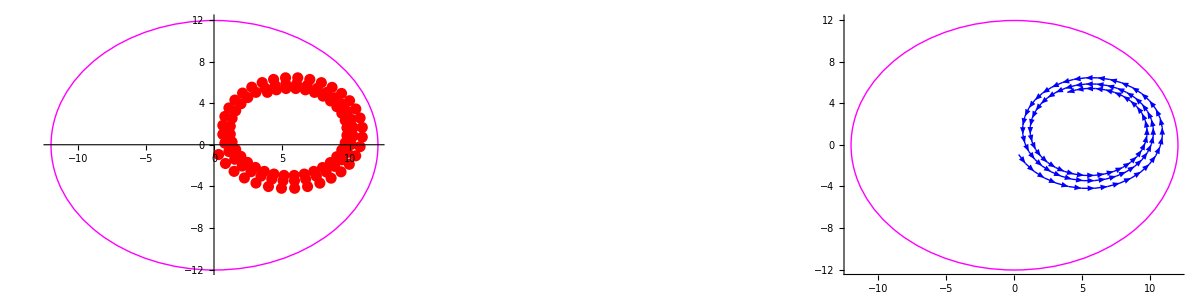

```mathematica
zr=12;
g1=ListPlot[t,PlotRange->{{-zr,zr},{-zr,zr}},AspectRatio->1,PlotStyle->{PointSize[0.02],Red},Epilog->{Magenta,Circle[{0,0},zr]}];
pt=Partition[N[t],2,1];
g2=Graphics[{Blue,Map[Arrow,pt],Magenta,Circle[{0,0},zr]},PlotRange->{{-zr,zr},{-zr,zr}},AspectRatio->1,Axes->True];
Grid[{{g1,Spacer[50],g2}}]
```

圆周上任取一点（z=1点除外）并任取一个不大于 1 的  q>0，

画  S_d=(n+1)^q S_p 随 p 从 1 增加时在复平面上的轨迹 ，其中：S_p=(∑_(k=1))^p z^(k+n)/(k+n)^q 为 Cauchy 判据中的量

再一次出现在某区域绕圈情况（参见上一节的例题）

暗示   (n+1)^q S_p 有界    ⟹   (n+1)^q|S_p|<M，故只需 n 足够大，即可满足|S_p|<ε

因为：(n+1)^q|S_p|<M，故   |S_p|<M/(n+1)^q<ε      ⟸    n>(M/ε)^(1/q)=N

也就是说： ∀ε>0，∃N=(M/ε)^(1/q)，使得 n>N 时，|S_p|<ε，满足 Cauchy 判据。

当然，以上并不构成数学证明，仅仅是一个启发。那么数学上如何利用 (n+1)^q|S_p|有界？

#### 当 z≠1 时（Dirichlet 判别法）

用 Dirichlet 判别法：若 a_k 随 k 增大单调变化且趋于 0， (∑_(k=1))^n b_k  对任意 n 有界，则级数  (∑_(k=1))^∞ a_k b_k  收敛

原级数为： S=(∑_(k=1))^∞z^k/k^q 在 q≤1， 取 a_k=1/k^q, b_k=z^k。      显然a_k 单调变化且趋于 0

b_k=z^k,        (⟹_(z = ⅇ^(ⅈ θ)))^(圆周上 |z|=1)   (∑_(k=1))^n b_k=(∑_(k=1))^n ⅇ^(ⅈ θ k)=(ⅇ^(ⅈ θ)(ⅇ^(ⅈ n θ)-1))/(ⅇ^(ⅈ θ)-1),  只要 θ≠0 就有界

故：当 0< q≤1时，S=(∑_(k=1))^∞z^k/k^q  对在圆周上 |z|=1，除了 z=1点是收敛的。

#### 为何要证明圆周上的点收敛：利用圆内的和函数表达式，求圆周上的级数和（Abel 第二定理）

#### 附：Dirichlet 判别法的证明

绕圈形式的处理 —— Dirichlet判别法：若 a_k  随着 k 的增大单调且趋向于 0， (∑_(k=1))^n b_k  对任意 n 有界，则级数 (∑_(k=1))^∞ a_k b_k  收敛

绕圈暗示着有界，因此将这类问题推广，就指向 Dirichlet 判别法。

原级数 S=(∑_(n=1))^∞z^k/k^q   在圆周上  1/k^q 与 z^k 分别是 Dirichlet 判别法中的 a_k  和 b_k

证明：

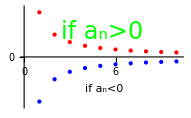
a_n  随着 n 的增大单调且趋向于0，
只有两种情况，如图。
不妨设 a_n>0，如红点所示。
考察Cauchy 判据中的量 S_p   
          S_p=(∑_(k=1))^p a_(n+k)b_(n+k)  -Graphics-

S_p=(∑_(k=1))^p a_(n+k)b_(n+k)             令  k=m+1
=(∑_(m=0))^(p-1)a_(n+m+1) b_(n+m+1)
=(∑_(m=0))^(p-1)a_(n+m+1) [b_(n+m+1)+b_(n+m)θ(m-1)]
                         -(∑_(m=1))^(p-1)a_(n+m+1) b_(n+m)θ(m-1)         其中 θ(x)={0, | x<0
1, | x≥0   —— Heaviside 阶跃函数
                                   这里用  θ(x) 表示当 m=0 时，不加减蓝色项：b_(n+m)
=(∑_(m=0))^(p-1)a_(n+m+1) [b_(n+m+1)+b_(n+m)θ(m-1)]-(∑_(m=0))^(p-2)a_(n+m+2) b_(n+m+1) (θ(m))^(⏞^(≡1))
=(∑_(m=0))^(p-1)a_(n+m+1) [b_(n+m+1)+b_(n+m)θ(m-1)+b_(n+m-1)θ(m-2)]-(∑_(m=0))^(p-2)a_(n+m+2) b_(n+m+1) 
                             -((∑_(m=2))^(p-1)a_(n+m+1) b_(n+m-1)θ(m-2))_(⏟_(这项  =(∑_(m=0))^(p-2)a_(n+m+2) b_(n+m)θ(m-1)))
=(∑_(m=0))^(p-1)a_(n+m+1) [b_(n+m+1)+b_(n+m)θ(m-1)+b_(n+m-1)θ(m-2)]-(∑_(m=0))^(p-2)a_(n+m+2)[ b_(n+m+1)+b_(n+m)θ(m-1) ]

以此类推。再令：L_m=b_(n+m+1)+b_(n+m)+…+b_(n+1)        这样做是为了把这一有界（绕圈）项分离出来

注意这里的 L_m 其实就是中括号部分

S_p=(∑_(m=0))^(p-1)a_(n+m+1)L_m-(∑_(m=0))^(p-2)a_(n+m+2)L_m,       接着，把第一项的 m=p-1项单独列出

S_p=(∑_(m=0))^(p-2)[a_(n+m+1)L_m-a_(n+m+2)L_m]+a_(n+p)L_(p-1)

|S_p|≤  (∑_(m=0))^(p-2)(a_(n+m+1)-a_(n+m+2))|L_m|+a_(n+p)|L_(p-1)| ,      因为 a_n>0 单调下降，(a_(n+m+1)-a_(n+m+2))>0

因为(∑_(k=1))^n b_k  对任意 n 有界，故 L_m 对任意 m 有界，即： |L_m|<l_max

|S_p|≤ l_max{(∑_(m=0))^(p-2)(a_(n+m+1)-a_(n+m+2))+a_(n+p)}     ⟹     |S_p|≤ l_max a_(n+1)

Cauchy 判据   |S_p|<ε    ⟸    a_(n+1)l_max<ε    ⟸    a_(n+1)<ε/l_max

因为 a_n>0  随着 n 单调下降，故 ∃ N，使得 n>N 时，a_(n+1)<ε/l_max

回到级数：(∑_(k=1))^∞z^k/k^q，a_k=1/k^q 满足 Dirichlet 判据的条件；b_k=z^k

现在剩下最后一步：需要证明 L_m= (∑_(n=1))^m b_n=(∑_(n=1))^m z^n 对任意的 m 有界。

从图像上看，L_m 是绕圈的，一定有界。

```mathematica
Lm[m_,ϕ_]:=Sum[ⅇ^(ⅈ k ϕ),{k,0,m}];
Sd[n_,ϕ_]:=Table[{Re[Lm[m,ϕ]],Im[Lm[m,ϕ]]},{m,0,n}];

ϕ0=10/(√2) Degree;
t=Sd[50,ϕ0];
```

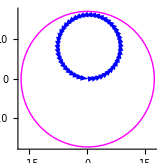

```mathematica
zr=1/Sin[ϕ0/2]+1;
pt=Partition[N[t],2,1];
g2=Graphics[{Blue,Map[Arrow,pt],Magenta,Circle[{0,0},zr]},PlotRange->{{-zr,zr},{-zr,zr}},AspectRatio->1,Axes->True]
```

从解析式上看：b_k=z^k,  z=ⅇ^(ⅈ ϕ),   L_m= (∑_(k=1))^m b_k

L_m=(∑_(k=1))^m ⅇ^(ⅈ k ϕ)  ⟹^等比级数   (ⅇ^(ⅈ ϕ)-ⅇ^(ⅈ (m+1)ϕ))/(1-ⅇ^(ⅈ ϕ))=(sin m/2 ϕ)/(sin ϕ/2)ⅇ^(ⅈ ((m+1)/2)ϕ),

|L_m|≤ 1/(sin ϕ/2),     对  0<ϕ<2π 的确是有界的。

## 3.3 解析函数的Taylor展开

幂级数在收敛圆内绝对且内闭一致收敛，据Weierstrass定理，其和函数是解析函数。

其实，我们更关心一个解析函数能否表为绝对且（内闭）一致收敛的幂级数，以便计算复积分。（一致收敛就可以保证能逐项求积分）

### 解析函数的Taylor展开定理

展开定理：设 f(z) 在以 b为圆心的一个圆域 |z-b|<R 内解析，则 f(z) 可在圆内任意点 z展开为在该圆内绝对收敛且内闭一致收敛的 Taylor级数

f(z)=(∑_(k=0))^∞ (a_k(z-b))^k=(∑_(k=0))^∞  (f^(k)(b))/(k!)(z-b)^k,    a_k=(f^(k)(b))/(k!)=1/(2π ⅈ)∳_C (f(ξ)ⅆξ)/(ξ-b)^(k+1),  C 为圆内包围 b 点的任意闭曲线

（展开式形式上与实变函数相同）该定理实际上包含了几个方面

1. 能否将一个解析函数写成幂级数形式？✓

2. 写成的幂级数在 |z-b|<R 内是否内闭一致收敛？绝对收敛？✓

3. 写成的幂级数是否唯一？✓

4. 幂级数的收敛半径如何？

这四个问题构成任意解析函数与幂级数之关系。下面就这四个方面加以证明。

1.  将解析函数表为幂级数

f(z)在区域  D：|z-b|<R 解析，
∀z∈D, 在区域  D 内以 b 点为圆心做一个圆 C_ρ, 
将 z 包围在圆内。应用Cauchy公式：
f(z)=1/(2π ⅈ)∳_C_ρ (f(ξ))/(ξ-z)ⅆξ,

注意 ξ 在 C_ρ 上，故：|ξ-b|>|z-b|   ⟹  |(z-b)/(ξ-b)|<1

f(z)=1/(2π ⅈ)∳_C_ρ (f(ξ))/((ξ-b)-(z-b))ⅆξ

f(z)=1/(2π ⅈ)∳_C_ρ 1/(1-((z-b)/(ξ-b)))(f(ξ))/(ξ-b)ⅆξ

f(z)=1/(2π ⅈ)∳_C_ρ (∑_(k=0))^∞((z-b)/(ξ-b))^k(f(ξ))/(ξ-b)ⅆξ

(|z-b|)/(|ξ-b|)<1,   (∑_(k=0))^∞((z-b)/(ξ-b))^k 在 C_ρ 上一致收敛，在 C_ρ 上 (f(ξ))/(ξ-b) 有界，

故 (∑_(k=0))^∞((z-b)/(ξ-b))^k(f(ξ))/(ξ-b) 在 C_ρ 上一致收敛，故求积分与求和可交换次序

f(z)=(∑_(k=0))^∞[1/(2π ⅈ)∳_C_ρ (f(ξ))/(ξ-b)^(k+1)ⅆξ](z-b)^k

f(z)=(∑_(k=0))^∞(a_k(z-b))^k,

a_k=[1/(2π ⅈ)∳_C_ρ (f(ξ))/(ξ-b)^(k+1)ⅆξ]=(f^(n)(b))/(n!)

回答了第一个问题：任意解析函数，在它的一个解析圆域内，

均可写成一圆心为中心的幂级数形式，该幂级数收敛于解析函数。

那么，级数是否一致收敛？

2.  幂级数在|z-b|<R 绝对收敛且内闭一致收敛。如何证明？寻找优级数。

幂级数的通项 ：w_k(z)=1/(2π ⅈ)∳_C_ρ ((z-b)^k f(ξ))/(ξ-b)^(k+1)ⅆξ

|w_k(z)|≤ 1/(2π)∳_C_ρ ((|z-b|)^k|f(ξ)|)/(|ξ-b|)^(k+1)|ⅆξ|，   C_ρ：|z-b|=ρ
下证明级数绝对且内闭一致收敛。
对任何|z-b|<R 之内的闭区域（如图蓝色区）
均可做一圆 |z-b|≤ R_1（如图黄色区）将其包围在内之内
而 |z-b|≤R_1 又在 |z-b|≤ρ（如图绿色区） 之内，
故蓝色闭区域内的任何点，均满足：|z-b|<R_1<ρ=|ξ-b|        -Graphics-

|w_k(z)|=|1/(2π ⅈ)∳_C_ρ ((z-b)^k f(ξ))/(ξ-b)^(k+1)ⅆξ|≤ 1/(2π)(R_1/ρ)^k 1/ρ∳_C_ρ |f(ξ)| |ⅆξ|

|w_k(z)|≤ (M(R_1/ρ))^k    这里 M 为 |f(z)|在 C_ρ 上的最大值。

⟹    (∑_(k=0))^∞(M(R_1/ρ))^k  是原级数 (∑_(k=0))^∞w_k(z)   的优级数，存在优级数，故幂级数绝对且内闭一致收敛。

故 f(z)可写成在 |z-b|<R 区域内绝对收敛且内闭一致收敛的幂级数。求积分与求和可交换次序。

3.  幂级数的唯一性

f(z)=(∑_(k=0))^∞(a_k(z-b))^k=(∑_(k=0))^∞(c_k(z-b))^k

因为级数内闭一致收敛，由Weierstrass定理，可逐项求导。

上两表达式逐项求导再令 z=b 即得 a_k=c_k

4. 幂级数的收敛半径 R

一般来说，R 为 f(z)离 b 最近的奇点 s 到 b 之距离 d=|s-b|

设 R<d：因 f(z)在|z-b|<d 解析，
f(z)的幂级数在|z-b|<d 区域内闭一致收敛，
在收敛圆外的绿、黄圆之间必存在一点 P
在 P 点 f(z) 解析，幂级数在 P 点上收敛于 f(z)
这与 P 点在收敛圆外（发散）矛盾。
设 R>d：由于幂级数在收敛圆内解析，
 故在圆周|z-b|=d <R 上，幂级数解析，
这与函数在圆周上有一奇点矛盾。    -Graphics-

综上：d=R

思考：如何排除以下可能性：存在这样一个幂级数，

在 |z-b|<d =|s-b|时等于解析函数 f(z)，s 是离 b 最近的奇点

但其收敛半径 R>|b-s|=d，即：在 d≤|z-a|<R，幂级数也收敛，但不等于 f(z)？

这里需涉及奇点的分类：若 s 是孤立奇点，可以证明不可能（可去奇点不作为奇点）。

（幂级数在收敛圆内是内闭一致收敛的，据 Weierstrass 定理，和函数 g(z) 解析，

在 |z-b|<d 有 g(z)=f(z)。若 s 是 f(z) 的孤立奇点，

则在 d<|z-b|<R，也一定有 g(z)=f(z)  ——  参见解析延拓一节）

复变函数f(z) 在 D 内解析，则它必有任意阶导数，故必可展开。

对实变函数 f(x)，一阶导数存在不能保证二阶导数一定存在，故不能保证一定可以某区间展开为 Taylor 级数。

在无穷远点邻域的展开：做变换 ζ=1/z，在 ζ=0 邻域展开。

### 展开方法 —— 基于唯一性

例题   在 z_0 的邻域展开称为Taylor级数（即：展为以 z_0 为中心的幂级数）

1.    f(z)=1/(1-z)^2 在 z_0=0 邻域展开

解：熟知  1/(1-z)=(∑_(k=0))^∞z^k      在 |z|<1 绝对收敛且内闭一致收敛

两边同时求导（可逐项求导）得

1/(1-z)^2=(∑ _(k=0))^∞k z^(k-1)=(∑ _(k=0))^∞(k+1) z^k

2.    f(z)=ln(1+z)/(1-z) 在 z_0=0 邻域展开 ，已知多值函数 f(0)=0

解：f'(z)=1/(1+z)+1/(1-z)=(∑_(k=0))^∞(-z)^k+(∑_(k=0))^∞z^k

f(z)=-(∑_(k=0))^∞(-z)^(k+1)/(k+1)+(∑_(k=0))^∞z^(k+1)/(k+1)+c
=(∑_(k=0))^∞z^k/k[1-(-1)^k]+c
=2(∑_(k=0))^∞z^(2k+1)/(2k+1)+c,     由 f(0)=0  ⟹  c=0

3.    f(z)=(z-1)/(z+1) 在 z_0=1 邻域展开

解：我们对在 z=0邻域展开较为熟悉，故令 t=z-1，g(t)=f(z)=t/(t+2)

g(t)=1/2 t/(1+t/2)=t/2  (∑_(k=0))^∞(-t/2)^k,   t=z-1 代入

f(z)=(∑_(k=0))^∞(-1)^k/2^(k+1)(z-1)^(k+1)，

收敛圆： |t/2|<1     ⟹     |z-1|<2。

离 z=1 最近的奇点为 z=-1，距离 2，故收敛半径为 2。

4.    f(z)=ⅇ^z/(1-z) 在 z_0=0 邻域展开

解：ⅇ^z 的 n 阶导数 (ⅇ^z)^(n)=ⅇ^z，直接应用Taylor展开公式，

可得：ⅇ^z=(∑_(m=0))^∞z^m/(m!),   全平面绝对且一致收敛
另：  1/(1-z)=(∑_(n=0))^∞z^n,  在  |z|<1  绝对且一致收敛
f(z)=(∑_(m=0))^∞z^m/(m!)(∑_(n=0))^∞z^n   ⟹^绝对收敛 (∑_(m=0))^∞(∑_(n=0))^∞z^(n+m)/(m!)      
应写成：    (∑_(k=0))^∞a_k z^k 形式 
引入新亚元 (k,l) ：{m=l
m+n=k ,   
把旧亚元表示为新亚元的函数    -Graphics-

{m=l
n=k-l    (⟹_可得到新亚元上下限不等式)^代入旧亚元的上下限不等式    {0≤m=l<∞
0≤ n=k-l<∞       如图阴影部分

f(z)=(∑_(m=0))^∞(∑_(n=0))^∞z^(n+m)/(m!)=(∑_(k=0))^∞ ((∑_(l=0))^k 1/(l!)) z^k,       a_k=(∑_(l=0))^k 1/(l!)

5.    f(z)=ⅇ^z cos z 在 z_0=0 邻域展开

解：可以分别展开在再 求乘积，另一种做法如下

ⅇ^z (cos z+ⅈ sin z)=ⅇ^(z+ⅈ z)=ⅇ^(√2 z ⅇ^(ⅈ π/4))
=(∑_(n=0))^∞((√2)^n ⅇ^(ⅈ n π/4))/(n!)z^n

ⅇ^z (cos z-ⅈ sin z)=ⅇ^(z-ⅈ z)=ⅇ^(√2 z ⅇ^(-ⅈ π/4))
=(∑_(n=0))^∞((√2)^n ⅇ^(-ⅈ n π/4))/(n!)z^n

两式相加，利用  ⅇ^(ⅈ n π/4)+ⅇ^(- ⅈ n π/4)=2 cos (n π)/4

ⅇ^z cos z=(∑_(n=0))^∞ (2^(n/2) cos (n π)/4)/(n!)z^n

6.    试利用Taylor展开验证：ⅇ^z_1 ⅇ^z_2=ⅇ^(z_1+z_2)

证明：ⅇ^z_1=(∑_(m=0))^∞ z_1^m/(m!),       |z_1|<∞ 绝对收敛

ⅇ^z_1 ⅇ^z_2=(∑_(m=0))^∞ z_1^m/(m!)(∑_(n=0))^∞ z_2^n/(n!)=(∑_(n=0))^∞(∑_(m=0))^∞ z_1^m/(m!) z_2^n/(n!)

引入新亚元 (k,l)： 
{m=l
m+n=k         把旧亚元表为新亚元
                               ⟹    {m=l
n=k-l   
由 {0≤m<∞
0≤ n<∞     ⟹     {0≤m=l<∞
0≤ n=k-l<∞        
如上题图中的阴影部分-Graphics-

ⅇ^z_1 ⅇ^z_2=(∑_(k=0))^∞ 1/(k!)((∑_(l=0))^k(k!)/(l!(k-l)!)z_1^l z_2^(k-l)) =(∑_(k=0))^∞ 1/(k!)(z_1+z_2)^k=ⅇ^(z_1+z_2)

7.    试将函数  f(z)=(1+z)^α 在 z=0 邻域展开为 Taylor 级数，知 f(0)=ⅇ^(2α ⅈ π)（α是复数）

解：实际上， f(z)=(1+z)^α=ⅇ^(α Ln (1+z))=ⅇ^(α [ ln|1+z|+ ⅈ arg(1+z) + ⅈ 2k π])

f(z)是多值函数，故题中告知 f(0)的值。

据定义，复幂函数：f(z)=ⅇ^(α Ln(z+1))，因 f(0)=ⅇ^(α 2π ⅈ)
故在 z=0点，arg(1+z)=2π，即复变量1+z 的辐角为 2π 
注：z+1 视为从 -1 到  z 的自由矢量（如图蓝色箭头）
利用Taylor展开公式，且
f(0)=ⅇ^(2α ⅈ π)      注意：在 z=0时 arg(z+1)=2π
f'(0)=(α(1+z))^(α-1)=α ⅇ^((α-1) Ln(z+1))=α ⅇ^((α-1)ⅈ 2π)=α ⅇ^(ⅈ 2α π)
f''(0)=α(α-1)(1+z)^(α-2)=α (α-1)ⅇ^((α-2) Ln(z+1))=α (α-1)ⅇ^(ⅈ 2 α π)
f^(k)(0)=α(α-1)...(α-k+1)ⅇ^(ⅈ 2 α π)   -Graphics-

直接应用 Taylor 展开公式：f(z)=(∑_(k=0))^∞(f^(k)(0))/(k！)z^k=ⅇ^(ⅈ 2 α π)[1+(∑_(k=1))^∞(α(α-1)...(α-k+1))/(k!)z^k]

如果 α 为正整数，总有一自然数 k 使得 (α-k+1)=0，展开式退化为有限项（二项式定理）

若 α=-1，则退化为熟知的  1/(1+z)=(∑_(k=0))^∞(-z)^k

多值性完全归结到 ⅇ^(ⅈ 2 α π)，其余部分是单值的。

收敛半径为 R = 1，z=-1 是支点，支点是奇点，并且是非孤立奇点（以后会讨论）。

(在圆心于原点的单位圆内，arg(1+z) =(arg(1+z))^ |)_(z=0) + θ

θ 为 z 从 z=0 在单位圆内到 z，矢量 z+1 转过的角度（逆时针正顺时针负）

8.    证明最大模定理，即：若 f(z) 在闭区域 Ḡ 上解析，则|f(z)|只能在 Ḡ 的边界上取极大值。

证明：反证法。设 |f(z)| 在 区域的某个内点 z_0 取极大值。

因为 z_0 是内点，必可找到一个邻域  C_δ： |z-z_0|≤δ，该邻域落在闭区域 Ḡ 内，从而该邻域解析。

f(z)在该邻域可 Taylor 展开：f(z)=(∑_(k=0))^∞(a_k(z-z_0))^k,    f(z_0)=a_0,   (|f(z_0)|)^2=(|a_0|)^2

现在求 (|f(z)|)^2 在以 z_0 为中心，ε 为半径的圆周（z-z_0=ε ⅇ^(ⅈ θ)）上的平均值   ⟨(|f(z)|)^2⟩

(|f(z)|)^2=f(z)f^*(z)=(∑_(k=0))^∞(a_k(z-z_0))^k(∑_(l=0))^∞(a_l^*[(z-z_0)^*])^l
=(∑_(k,l))^∞a_k a_l^* ((z-z_0)^k[(z-z_0)^*])^l  （利用了绝对收敛性质）
⟨ (|f(z)|)^2⟩=1/(2π)∫_0^(2π) (|f(z)|)^2 ⅆθ=1/(2π)∫_0^(2π) (∑_(k,l))^∞a_k a_l^* ε^(k+l)ⅇ^(ⅈ (k-l)θ) ⅆθ,
=1/(2π)(∑_(k,l))^∞a_k a_l^* ε^(k+l)∫_0^(2π) ⅇ^(ⅈ (k-l)θ) ⅆθ    利用了一致收敛求积求和对调
=(∑_(k,l))^∞a_k a_l^* ε^(k+l)δ_(k,l)=(∑_(k=0))^∞(|a_k|)^2 ε^(2k)=(|a_0|)^2+(∑_(k=1))^∞(|a_k|)^2 ε^(2k)≥(|a_0|)^2=(|f(z_0)|)^2   -Graphics-

但 (|f(z_0)|)^2 是极大值，大于号不可能成立，只能是等号成立，

也就是说，对 z∈C_ε,   |f(z)|=|f(z_0)|。让 ε 从 0 变到 δ，均有： |f(z)|=|f(z_0)|

表明在 z_0 邻域 |z-z_0|≤δ，均有 |f(z)|=|f(z_0)|。

从而在 C_δ 内|f(z)|为常数，即 f(z) =f(z_0)为常数。（模为常数的解析函数必为常数）

g(z)=f(z)-f(z_0) 在 C_δ 内为零，而解析函数的零点是孤立的，除非这个函数恒为零。

故除非函数 f(z)=f(z_0)为常数，否则 |f(z)| 不可能在解析区的内点取极大值。

## 3.4 解析函数的Laurent展开

Taylor展开是解析函数在解析点邻域的展开，Laurent展开则是在奇点附近（去心邻域）的展开，

对奇点，要求函数在奇点存在一个去心邻域，在该去心邻域内函数单值解析。

或者，干脆挖去一个有限大小的圆，找一个环域，使得在环域内函数单值解析

注意：无论是 Taylor 或是 Laurent，展开仅在解析区进行，故对后者，奇点必须挖去。

### Laurent展开定理

展开定理：设 f(z) 在以 b为圆心的一个环形区域   R_2<|z-b|<R_1 内单值解析，则 f(z) 可在环域内的任意点 z可展为以 z=b为中心的 Laurent 级数

f(z)=(∑_(k=-∞))^∞ (a_k(z-b))^k,    a_k=1/(2π ⅈ)∳_C_ρ (f(ξ)ⅆξ)/(ξ-b)^(k+1)≠ (f^(k)(b))/(k!),  C_ρ 为环域内包围内圆的任意闭曲线。

类似于Taylor展开定理，Laurent展开定理实际上也包含以下几个方面

1. 环域内 f(z) 能写成 Laurent 级数形式；✓

2. Laurent级数在环域  R_2<|z-b|<R_1 里内闭一致收敛；✓

3. Laurent级数是唯一的；✓

4. Laurent级数的收敛范围（区域）如何？（这里不是幂级数，不问收敛半径如何。）

—— 其实这个第 4 问在第 2 问中已经回答了。

下面就这几个方面加以证明。

1. 和 2.  一同解决

在环域R_2<|z-b|<R_1里表为内闭一致收敛的Laurent级数

f(z)在复连通环域 D：R_2<|z-b|<R_1 解析，即在 R_2<ρ_2≤|z-b|≤ρ_1<R_1 解析

相当于“内闭解析”（当然数学上无需这个概念，想一想为什么）

∀z∈D, 应用复连通Cauchy公式
                     （注意 z 在闭区域 ρ_2≤|z-b|≤ρ_1  之内）
2π ⅈ f(z)=(∳_C_ρ_1 (f(ξ))/(ξ-z)ⅆξ)^(⏞^I_1)+(∲_C_ρ_2 (f(ξ))/(ξ-z)ⅆξ)^(⏞^I_2),
I_1=∳_C_ρ_1 (f(ξ))/(ξ-b-(z-b))ⅆξ     展开并交换求和、积分次序
=(∑_(k=0))^∞∳_C_ρ_1 (f(ξ)(z-b)^k)/(ξ-b)^(k+1)ⅆξ       将积分路径变形
=(∑_(k=0))^∞∳_C_ρ (f(ξ)(z-b)^k)/(ξ-b)^(k+1)ⅆξ       利用了 ∳_C_ρ_1 ⟹ ∳_C_ρ -Graphics-

=(∑_(k=0))^∞ a_k(z-b)^k,       a_k=1/(2π ⅈ)∳_C_ρ (f(ξ)ⅆξ)/(ξ-b)^(k+1)     注意 C_ρ 是环域内包围内圆的闭合路径，如图紫色线

Clearly,obviously,evidently,it is easy to see,it is not difficult to see,it is plain that, it is readily seen that

I_1 在 |z-b|<R_1 区域里内闭一致收敛

（怎么证明？优级数，证明类似于 Taylor 展开）在积分路径变形前的(∑_(k=0))^∞∳_C_ρ_1 上证明

If you don't  agree that it is clear,obvious,and evident,turn back a few pages and make a fresh start

I_2=∲_C_ρ_2 (f(ξ))/(ξ-b-(z-b))ⅆξ      （注意积分路径走向：内边界顺时针）
=-1/(z-b)∲_C_ρ_2 (f(ξ))/(1-((ξ-b)/(z-b)))ⅆξ         在 C_ρ_2 上积分，|ξ-b|<|z-b|
=-1/(z-b)(∑_(k=0))^∞∲_C_ρ_2 f(ξ)((ξ-b)/(z-b))^k ⅆξ              改变积分走向
=(∑_(k=0))^∞∳_C_ρ_2 (f(ξ))/(ξ-b)^(-k-1+1)(z-b)^(-k-1)ⅆξ ,  令 k'=-k-1，且积分路径 C_ρ_2 变形至 C_ρ
=(∑_(k'=-1))^(-∞)∳_C_ρ (f(ξ))/(ξ-b)^(k'+1)(z-b)^k' ⅆξ

I_2 在 |z-b|>R_2 区域里内闭一致收敛 （Clearly,obviously,evidently,readily seen …）

联立 I_1 和 I_2 即得Laurent展开式，级数在环域 R_2<|z-b|<R_1 内闭一致收敛。

f(z)=(∑_(k=-∞))^∞ [1/(2π ⅈ)∳_C_ρ (f(ξ)ⅆξ)/(ξ-b)^(k+1)](z-b)^k

3.  唯一性

在环域里内闭一致收敛，级数可逐项求导、求积

设 f(z)有另一个也是内闭一致收敛的Laurent展开式：

f(z)=(∑_(k=-∞))^∞ (c_k(z-b))^k  =(∑_(n=-∞))^∞ (a_n(z-b))^n

与Taylor展开不同，b 点可能不解析，不能用 z=b 带入证明 a_k=c_k。

可从Laurent展开的系数表达式出发

a_n=1/(2π ⅈ)∳_C_ρ (f(z)ⅆz)/(z-b)^(n+1)    把 (1.EquationNumbered)式 f(z)=(∑_(k=-∞))^∞ (c_k(z-b))^k  带入并逐项求积
=1/(2π ⅈ)(∑_(k=-∞))^∞∳_C_ρ (c_k(z-b))^k/(z-b)^(n+1)ⅆz=1/(2π ⅈ)(∑_(k=-∞))^∞c_k∳_C_ρ (z-b)^(k-n-1)ⅆz
=1/(2π ⅈ)(∑_(k=-∞))^∞c_k 2π ⅈ δ_(k,n)=c_n

当 n>0 时，与Taylor展开不同，Laurent展开系数

a_n=1/(2π ⅈ)∳_C_ρ (f(ξ))/(ξ-b)^(n+1)ⅆξ≠(f^(n)(b))/(n!)

因为f(z)在 z=b 点可能不解析，f^(n)(b) 不存在。

那么，如果f(z)在  z=b 点解析，是否有  a_n=(f^(n)(b))/(n!)，No！

反例：

f(z)=1/(1-z^2)在环域 1<|z|<2 展为以 z=0 为中心的 Laurent 级数

1/(1-z^2)=-1/z^2 1/(1-1/z^2)=-(∑_(k=0))^∞1/z^(2k+2)=(∑_(k=-∞))^∞a_k z^k   （一般形式）

对应于对任意 k>0， a_k=0，但  (f^(k)(0))/(k!)=1/2[1+(-1)^k]≠a_k

以 b 点为中心的Laurent级数含有负幂次项，则 b 点一定是奇点吗？

如果f(z)在 |z-b|<R_1区解析，

Laurent级数必退化为Taylor级数，负幂次项系数必为 0，

然而，放反过来，尽管 Laurent级数含负幂次项，并不意味着 b 是奇点。

反例：

函数 1/(1-z^2)在z=0点解析，在环域 1<|z|<2

展开为以 z=0 为中心的Laurent级数：1/(1-z^2)=-(∑_(k=0))^∞1/z^(2k+2)，    1<|z|<2    仅含负幂次

为何含有负幂次，而函数却可能是解析的？

因为该例的展开仅在环域 1<|z|<2成立，在此环域的展开当然不能用于判断 z=0 的解析性

要判断 z=0 的解析性，必须在 z=0 的邻域  0<|z|<1 展开：

1/(1-z^2)=(∑_(k=0))^∞z^(2k)， 0<|z|<1，都是正幂次，

要通过是否有负幂次项判断 b 点是否奇点，应在 b 点的（去芯）邻域展开。

在 b 点去心邻域 0<|z-b|<δ 的Laurent展开才能表征函数在  b 点的奇异性

通常，若选取 b 点为中心，
f(z) 在复平面上的奇点（图中红色点）把复平面
分成以 b 点为中心的一个个环形解析（开）区域，
在每个环形解析区域内函数都可以做Laurent展开，
但只有在 b 点（去心）邻域
     0<|z-b|<δ 的Laurent展开
可“用于”判断函数在 b 点的奇异或解析性质。 -Graphics-

### 展开方法 —— 基于唯一性

例题    f(z)=1/((z-1)(z-2))以 z=1为中心作Laurent展开。

解：以 z=1为中心，令 t=z-1,  f(z)=1/t 1/(t-1),

z=1,2  两个奇点把复平面分成两个环域，

分别在  0<|z-1|<1 和 1<|z-1|<∞ 两环域展开

0<|z-1|<1 环域，|t|=|z-1|<1

f(z)=-1/t 1/(1-t)=-1/t(∑_(k=0))^∞t^k
=-(∑_(k=0))^∞(z-1)^(k-1)

1<|z-1|<∞ 环域，|t|=|z-1|>1

f(z)=1/t 1/(t-1)=1/t^2 1/(1-1/t)=1/t^2(∑_(k=0))^∞t^-k
=(∑_(k=0))^∞(z-1)^(-k-2)

例题    I=ⅇ^(t/2(z-z^-1))=exp[t/2(z-z^-1)] 作Laurent展开。

解：利用指数函数展开公式：

ⅇ^z=(∑_(k=0))^∞z^k/(k!)    收敛区： |z|<∞  （绝对且内闭一致收敛）

ⅇ^(t z/2)=(∑_(k=0))^∞1/(k!)((t  z)/2)^k=(∑_(k=0))^∞1/(k!)(t/2)^k z^k                 收敛区 |z|<∞ （全复平面）

ⅇ^(- t /2z)=(∑_(l=0))^∞1/(l!)(-t/(2z))^l=(∑_(l=0))^∞1/(l!)(-t/2)^l z^-l       收敛区  0<|z|<∞

I=(∑_(k=0))^∞(∑_(l=0))^∞(-1)^l/(k!l!)(t/2)^(k+l)z^(k-l)     这里利用了绝对收敛性质：(∑_(k=0))^∞u_k(∑_(l=0))^∞v_l=(∑_(k=0))^∞(∑_(l=0))^∞u_k v_l

但展开式通常希望写成 ∑_n a_n z^n 形式，为此，令：{k-l=n
l=m

引入了新求和变量 m, n。接着，将旧变量(k,l)表为新变量(m,n)的函数：{k=n+m
l=m

再由旧变量的变化范围得到新变量的变化范围： {0≤ l=m<∞
0≤ k=m+n<∞

新变量 m, n 变化范围： {0≤ m<∞
0≤ m+n<∞  如图阴影部分

故 I 需要分成两项： 其中{k=n+m
l=m
I=(∑_(k=0))^∞(∑_(l=0))^∞(-1)^l/(k!l!)(t/2)^(k+l)z^(k-l)=∑_n ∑_m a_n z^n, 
=((∑_(n=-∞))^-1(∑_(m=-n))^∞(-1)^m/((m+n)!m!)(t/2)^(n+2m)z^n)_(⏟_I_1) 
              + ((∑_(n=0))^∞ (∑_(m=0))^∞(-1)^m/((m+n)!m!)(t/2)^(n+2m)z^n)_(⏟_I_2)-Graphics-

I_2=(∑_(n=0))^∞J_n(t)z^n,  其中 Bessel 函数 J_n(x)定义为

J_n(x)≡(∑_(m=0))^∞(-1)^m/(m!(n+m)!)(x/2)^(n+2m), n>0,   Bessel函数的级数表示

I_1=(∑_(n=-∞))^-1(∑_(m=-n))^∞(-1)^m/((m+n)!m!)(t/2)^(n+2m)z^n=(∑_(n=1))^∞(∑_(m=n))^∞(-1)^m/((m-n)!m!)(t/2)^(2m-n)z^-n
=(∑_(n=1))^∞J_-n(t)z^-n, 其中 Bessel 函数 可定义为

J_-n(x)≡(∑_(m=n))^∞(-1)^m/(m!(m-n)!)(x/2)^(2m-n),    n>0
=(∑_(m=0))^∞(-1)^m/(m!(m-n)!)(x/2)^(2m-n),    
      其中约定对 k<0：1/(k!)=0（当然这个约定与以后要遇到的 Γ 函数的性质是一致的）

(1.EquationNumbered)和(1.EquationNumbered)式可视为 n>0和 n<0 时Bessel函数的定义（n=0时二者一致）。

联立 (1.EquationNumbered)和(1.EquationNumbered)式，写成一个表达式：

J_n(x)≡(∑_(m=0))^∞(-1)^m/(m!(n+m)!)(x/2)^(n+2m),   n 为整数，并约定 k<0 时，1/(k!)=0

故：I=I_1+I_2      ⟹          exp[t/2(z-z^-1)] =(∑_(n=-∞))^∞J_n(t)z^n

I=exp[t/2(z-z^-1)] 称为Bessel函数的生成函数。

生成函数：将其做 Laurent 展开，展开系数是一个特殊函数，则称之为该特殊函数的生成函数。

(遇到的另一个例子是 Hermite 多项式：g(t,z)=e^(2t z-z^2)=(∑_(n=0))^∞ (∂^n g(t,z))/(∂z^n)|)_(z=0)z^n/(n!) =(∑_(n=0))^∞H_n(t)z^n/(n!)

J_-n(x)和 J_n(x)之间有何关系？  看 J_-n(x) 是怎么来的。

由(1.EquationNumbered)：I_1≡(∑_(n=1))^∞(∑_(m=n))^∞(-1)^m/((m-n)!m!)(t/2)^(2m-n)z^-n=(∑_(n=1))^∞J_-n(t)z^-n

令：{n=k
m-n=l  引入新的求和变量 l, k 并把旧变量表为新变量： {n=k
m=k+l

{1≤ n<∞
n≤ m<∞   ⟹    {1≤ n=k<∞
k≤ m=k+l<∞

新变量 l, k 变化范围如上图阴影部分，
故：I_1=(∑_(n=1))^∞(∑_(m=n))^∞(-1)^m/((m-n)!m!)(t/2)^(2m-n)z^-n
=(∑_(k=1))^∞(∑_(l=0))^∞(-1)^(k+l)/(l!(k+l)!)(t/2)^(2l+k)z^-k    利用(1.EquationNumbered)
=(∑_(k=1))^∞(-1)^k J_k(t)z^-k=(∑_(n=1))^∞J_-n(t)z^-n    -Graphics-

由展开的唯一性：⟹   J_-n(x)=(-1)^n J_n(x),

当然，也可直接从定义(1.EquationNumbered) 和 (1.EquationNumbered)出发：

J_n(x)≡(∑_(m=0))^∞(-1)^m/(m!(n+m)!)(x/2)^(n+2m)， J_-n(x)≡(∑_(m=n))^∞(-1)^m/(m!(m-n)!)(x/2)^(2m-n)

J_-n(x)≡(∑_(m=n))^∞(-1)^m/(m!(m-n)!)(x/2)^(2m-n)   令：m-n=m'
=(∑_(m'=0))^∞(-1)^(m'+n)/(m'!(m'+n)!)(x/2)^(2 m'+n)=(-1)^n(∑_(m=0))^∞(-1)^m/(m!(m+n)!)(x/2)^(2m+n)=(-1)^n J_n(x)

看起来似乎毫无关系的 J_n(x) 与 J_-n(x) 其实是线性相关的。这个性质在求解微分方程中很重要。

例题   试证明

J_n(x)=1/(2π)∫_0^(2π) cos(n θ-x sinθ)ⅆθ     Bessel函数的积分表示

证：由Bessel函数的生成函数知

f(z)=ⅇ^(x/2(z-z^-1))=(∑_(n=-∞))^∞J_n(x)z^n

由 Laurent 展开公式：f(z)=(∑_(k=-∞))^∞ (a_k(z-b))^k,    a_k=1/(2π ⅈ)∳_C_ρ (f(ξ)ⅆξ)/(ξ-b)^(k+1)

J_n(x)=1/(2π ⅈ)∳_C (f(z))/z^(n+1)ⅆz=1/(2π ⅈ)∳_C (ⅇ^((x/2)(z-z^-1)))/z^(n+1)ⅆz，

取 C 为圆心于原点的单位圆，z=ⅇ^(ⅈ θ)

J_n(x)=1/(2π)∫_0^(2π) ⅇ^(ⅈ x sin θ)/ⅇ^(ⅈ n θ) ⅆθ=1/(2π)∫_0^(2π) ⅇ^(ⅈ (x sin θ-n θ))ⅆθ
=1/(2π)∫_0^(2π) cos(x sinθ-n θ)ⅆθ+ⅈ/(2π)∫_0^(2π) sin(x sin θ-n θ)ⅆθ

利用函数的周期性：∫_0^(2π) sin(x sin θ-n θ)ⅆθ=∫_-π^π sin(x sin θ-n θ)ⅆθ=0 （被积函数是奇函数）

J_-n(x)=1/(2π ⅈ)∳_C (ⅇ^((x/2)(z-z^-1)))/z^(-n+1)ⅆz，

再令：z=-ⅇ^(ⅈ θ), ⅆz=-ⅈ ⅇ^(ⅈ θ)ⅆθ

J_-n(x)=(-1)^n/(2π)∫_0^(2π) ⅇ^(-ⅈ x sin θ)/ⅇ^(- ⅈ n θ) ⅆθ=(-1)^n/(2π)∫_0^(2π) ⅇ^(ⅈ (n θ- x sin θ)) ⅆθ
=(-1)^n/(2π)∫_0^(2π) cos(n θ-x sin θ)ⅆθ+((-1)^n ⅈ)/(2π)∫_0^(2π) sin(n θ-x sin θ)ⅆθ
=(-1)^n J_n(x)

本例说明：特殊函数的性质可以从许多不同的表示（级数表示、积分表示 ）出发予以证明。

Bessel 函数的积分表示： J_n(x)=1/(2π)∫_0^(2π) cos(n θ-x sinθ)ⅆθ=1/(2π)∫_0^(2π) ⅇ^(ⅈ (x sin θ-n θ))ⅆθ = 1/(2π)∫_-π^π ⅇ^(ⅈ (x sin θ-n θ))ⅆθ

例题   f(z) 在环域 ρ<|z|<1/ρ,  (0<ρ<1)内解析，且 f(1/z^*)=f^*(z)。在该环域 f(z) 展开为以

z=0为中心的Laurent级数： f(z)=(∑_(n=-∞))^∞a_n z^n，试证：a_-n=a_n^*，并且在 |z|=1，f(z)为实数。

（注：1/z^* 和 z 是单位圆的一对对称点）

证：(∑_(n=-∞))^∞a_n z^n=f(z)=[f(1/z^*)]^*=[(∑_(n=-∞))^∞(a_n(1/z^*))^n]^*=(∑_(n=-∞))^∞a_n^*z^-n=(∑_(n=-∞))^∞a_-n^*z^n

由展开的唯一性：a_n=a_-n^*    ⟹   a_-n=a_n^*      ⟹      a_0为实数

|z|=1时，1/z=z^*,

f(z)=(∑_(n=-∞))^∞a_n z^n=a_0+(∑_(n=1))^∞(a_n z^n+a_-n z^-n)
=a_0+(∑_(n=1))^∞[a_n z^n+(a_-n(z^*))^n]=a_0+(∑_(n=1))^∞[a_n z^n+(a_n^*(z^*))^n]=实数

思考：f(1/z^*) 是否显含 z^*，貌似不满足 C-R 条件，还能做 Taylor 展开f(1/z^*)=(∑_(n=-∞))^∞(a_n(1/z^*))^n 吗？

## 3.5 解析函数的零点和孤立奇点

由上一节知，奇点附近的展开应该是在奇点附近找一解析环域，在该环域（或去心圆域）做Laurent展开。

这就要求函数在奇点附近存在解析区（解析环域）。数学上如何描述所谓奇点附近存在解析区？

因为奇点很多时候是由于分母出现零点，因此让我们先看看关于零点有哪些特性。

### 解析函数的零点及其孤立性

定义：f(z)在 b点解析且 f(b)=0，则称 b为解析函数 f(z)的零点。

零点的阶数：Taylor 展开的最低幂次。

据解析的定义，在 b 点解析，必∃δ, 使得 在 0≤|z-b|<δ 解析 ，故可以Taylor展开：f(z)=(∑_(k=0))^∞(a_k(z-b))^k,

f(b)=0,   故：a_0=0。a_1=0?

若 a_1=a_2=...=a_(m-1)=0,   则称 b 为 m 阶零点 —— Taylor 展开的最低幂次 为 m 次

若 b 为 m 阶零点，由：f(z)=(∑_(k=m))^∞(a_k(z-b))^k  和  a_k=(f^(k)(b))/(k!),    记得 f(z) 最低幂次为 m，a_k=0, k=0,1,...,m-1

得：f^(k)(b)=0  for  k=0,1,2,...,m-1，f^(m)(b)≠0。

m 阶 0点含义：函数在 b 点的函数值和低阶导数值均为 0，直到 m 阶导数才为非 0

零点的孤立性

设 b 为f(z)的零点，若f(z)在 z=b 点解析且不恒为零，则必存在某个邻域 |z-b|<δ，在该邻域内除 b 点外，f(z)≠0。

证明：因为 f(z)在 z=b 点解析，必可做 Taylor 展开，设 b 为 m 阶零点，则

f(z)=(∑_(k=m))^∞(a_k(z-b))^k
          =(z-b)^m[a_m+a_(m+1)(z-b)+...]=(z-b)^m φ(z),
φ(b)=a_m≠0
由于 f(z)解析，幂级数 φ(z) 必一致收敛，故 φ(z)必连续
即 ∀ε>0, ∃ρ,  使得当 |z-b|<ρ 时，|φ(z)-a_m|<ε.
现取 ε=|a_m|/2，必存在 δ，使得当 |z-b|<δ 时，       -Graphics-

|φ(z)-a_m|<ε=|a_m|/2   ⟹   |a_m|-|φ(z)|<|a_m|/2    ⟹    |φ(z)|>|a_m|/2>0

即 ∃一个 δ 邻域，在该邻域内， |φ(z)|>0,   而在 去心邻域  0<|z-b|<δ,  (z-b)^m≠0,

故在 b 点的去心邻域   0<|z-b|<δ，f(z)=(z-b)^m φ(z)≠0

⟹    解析函数的零点是孤立的。除非该函数恒为零（任意阶导数均为 0）。

例：已知 f(z) 在 z=1/n 时，f(1/n)=(1+(-1)^n)/(2n),  n=1,2,3,…，试问 f(z) 在 z=0 是否解析？

解： f(z) 在z=z_0=0点不解析，以下用反证法证之。

反证法的思路是：先证在 z_0=0 点极限为 0，进而函数值为 0。再证 z_0=0非孤立。

若 f(z) 解析，则函数连续，必有 lim_(z→0) f(z)=f(0)  （极限存在且等于函数值）

z 无论以何种方式趋于 0，极限都要存在且相等，假设极限值为 lim_(z→0) f(z)=f_0。

以下证   lim_(z→0) f(z)=f_0=0   （注意解析函数极限必定存在）

反证：假设 f_0≠0，∀ε, ∃ δ，在 |z-z_0|<δ 时，|f(z)-f_0|<ε （任意小）

但在 |z-z_0|<δ 区域里有许多点 z_n=1/(2n+1)处 f(z_n)=0，

|f(z_n)-f_0|=|f_0|  不可能小于任意小

故 f(z) 在 z_0 点若存在极限，其极限值只能为 0，即：f_0=0

又因为 f(z)连续，f(0)=f_0，故在 z_0=0点函数值为 0。故 z=0 是 f(z) 的零点。

另一方面，当 n 为奇数时 f(1/n)=(1+(-1)^n)/(2n)=0，即： f(z_n)=0，z_n=1/(2n+1)

即 z_0 的任意一个邻域内都存在许多的 0 点，即 z=0 是非孤立零点。f(z) 在 z=0 不可能解析。

是否存在满足 f(1/n)=f(-1/n)=1/n^2, n=1,2,3,… 且在 z=0 解析的函数 f(z) ? 若存在，f(z)=? （存在，f(z)=z^2）

### 孤立奇点

奇点：不解析的点，没有定义（如：分母为零）的点，多值函数的支点（以后会讨论），都是函数的奇点。

定义：设 b点是函数f(z)的奇点，若存在一个 δ>0，使得函数在去心邻域  0<|z-b|<δ内解析，则称 b点是函数f(z)的孤立奇点。

为何要特别讨论？因为对孤立奇点，即可以在 b 点的去心邻域（环域解析区  0<|z-b|<δ ）内做 Laurent 展开。

f(z)=ⅇ^z/(z-1)在 z=1点是孤立奇点， (sin z)/z 在 z=0点是孤立奇点

非孤立奇点：找不到一个邻域，使得在该邻域内，除了b点外处处解析（奇点进入 b 点的任何领域）

f(z)=1/(sin 1/z)在 z=0点不是孤立奇点，因为 z=1/(n π)都是 f(z) 的奇点，
 也即，无论多么小的 δ，都不能保证在 0<|z|<δ 内除了 z=0外都解析。
实际上，在 0<|z|<δ 之内还有奇点  z=1/(n π)  with   n>1/δ。

f(z)=1/(1+ⅇ^z)在 z=∞也是非孤立奇点，即不能找到一个邻域 |z|>M  （此式表示无穷远点的邻域）

使得在该邻域内不再有其它奇点。即：不可能做一个大圆，使得圆外除∞ 外无其它奇点。

例如，当 m 走够大时，奇点 z_m=ⅈ (2m+1)π  落入 z=∞的邻域  |z_m|>M。

当然，也可以经过变量代换 t=1/z，讨论函数在 t=0邻域的奇点孤立性。

f(z)=1/(1+ⅇ^(1/t)),   取 t=-ⅈ/((2k+1)π), 奇点可以离  t=0 任意近。

孤立奇点：离该奇点最近的另一奇点到该奇点的距离大于某个非零正值。

对孤立奇点 b，因为存在以内径为 0 的环域解析区，故一定可以在环域解析区  0<|z-b|<δ 进行 Laurent 展开。

f(z)=(∑_(k=-∞))^∞(a_k(z-b))^k,            0<|z-b|<δ      （绝对收敛且内闭一致收敛）

### 孤立奇点的分类

孤立奇点的分类：就是不仅要将函数的“天生一个仙人洞”给“曝光”出来，还要研究“洞中滴沥几何深”。

定义：对孤立奇点 b，在其解析的去心邻域作 Laurent 展开  （注意展开一定是在解析区进行的）

f(z)=(∑_(k=-∞))^∞(a_k(z-b))^k,            0<|z-b|<δ

若展开式中没有负幂次项，则奇点 b 称为可去奇点

若展开式中只有有限个负幂次项，则称为极点（pole），最负幂次到 -m 次，称 m  (m>0) 阶极点

极点阶数：Laurent 展开的最低负幂次

无限个负幂次项，则称本性奇点

为何要分类，至少，因为绕奇点 b 积分的计算与奇点的种类有关。那么，如何判别是哪一类奇点？

可去奇点的充要条件： |f(z)| 在 b 点的邻域有界。

必要性：可去奇点，Laurent 展开式没有负幂次项

f(z)=(∑_(k=0))^∞(a_k(z-b))^k,  因为 Laurent 展开是内闭一致收敛，

求极限与求和可交换次序： lim_(z→b) f(z)=a_0

接着，利用极限的 ε-δ 定义，∀ε>0, ∃δ,  使得 |z-b|<δ 时，

|f(z)-a_0|<ε  ⟹  |f(z)|-|a_0|<ε  ⟹ |f(z)|< |a_0|+ε    有界。

充分性： |f(z)| 在 b 点的某个 δ 邻域有界，由 Laurent 展开

f(z)=(∑_(k=-∞))^∞(a_k(z-b))^k,      a_k=1/(2π ⅈ)∳_C_ε (f(ξ)ⅆξ)/(ξ-b)^(k+1)

接着证明 k<0 时的 a_k=0。由 a_k 表达式知，需证明一个复积分为 0

取积分回路 C_ε 为落在 b 点的 δ 邻域内的小圆，ξ-b=ε ⅇ^(ⅈ θ),  ε≤ δ

则在积分回路上 |f(ξ)| 有界：|f(ξ)| <M,

|a_k|=1/(2π)|∳_C_ε (f(ξ)ⅆξ)/(ξ-b)^(k+1)|
≤1/(2π)∳_C_ε (|f(ξ)||ⅆξ|)/(|ξ-b|)^(k+1)
≤ M/ε^k  （积分圆 C_ε 的半径可任意小）

对 k<0,   |a_k|≤ M ε^-k 可小于任意小数，即：a_k=0   ⟹   无负幂次项。

对可去奇点，f(z)=(∑_(k=0))^∞(a_k(z-b))^k,    0<|z-b|<δ

(lim_(z→b) f(z)=a_0,  若重新规定 f(z)|)_(z=b)=a_0=lim_(z→b) f(z),

(则 f(z) 可视为在 b 点解析。思考：重新定义 f_(z)|)_(z=b)仅保证连续，为何就解析了？

（知否？知否？应是例题一个：若一些可能的非解析点落在一条线段上且在这些点连续，则这些连续点也解析）

例如：f(z)=(sin z)/(π-z),   lim_(z→π) f(z)=1,

定义  f(z)=Piecewise[{{(sin z)/(π-z), z≠π}, {1, z=π}}],    f(z) 在 z=π 解析。

故曰 可去奇点。

可去奇点通过连续性重新定义函数值，得到的新函数在可去奇点上是解析的（不仅仅是连续）。

邻域有界必有极限：若函数在点 b 的解析去心邻域 0<|z-b|<δ 内有界，则极限 lim_(z→b) f(z) 存在。

极点的充要条件：lim_(z→b) f(z) =∞    严格意义上无穷大归为极限不存在，

因此在这里等式 lim_(z→b) f(z) =∞ 的意义是：

∀M>0，∃ δ，使得当 |z-b|<δ 时，|f(z)|>M

语言描述：无论 z 以何种方式趋于 b ，f(z) 都趋于无穷远，|f(z)| 都趋于无穷大。

必要性：m 阶极点，Laurent展开式为

f(z)=(a_-m)/(z-b)^m+(a_(-m+1))/(z-b)^(m-1)+...+a_0+a_1(z-b)+...
=1/(z-b)^m[a_-m+a_(-m+1)(z-b)+...],    a_-m≠0

显然，无论 z 以何种方式趋于b，

只要离 b 足够近，|f(z)|必可大于任意正数。

充分性：应该证明：若 z→b 时，f(z)→∞ ，则 b 为极点。

令：g(z)=1/(f(z)),  显然：lim_(z→b) g(z)=0    故在 z 点的邻域，g(z) 有界，

故一定可找到一个 δ 邻域，使得 |z-b|<δ 时，|g(z)|<M

因此，z=b 是 g(z)的可去奇点（见可去奇点的充要条件）。

g(z)的Laurent展开式没有负幂次项，又  lim_(z→b) g(z)=0    ⟹    a_0=0,

g(z)=(a_m(z-b))^m+(a_(m+1)(z-b))^(m+1)+...，    m≥1, a_m≠0
=(z-b)^m[a_m+a_(m+1)(z-b)+...]=(z-b)^m φ(z)

(因级数内闭一致收敛，φ(z)在 b 邻域解析并且 φ_(z)|)_(z=b)=a_m≠0

故必存在一个邻域，在该领域 φ(z)≠0，故可求其倒数：ψ(z)=1/(φ(z))，

(ψ(z)=1/(φ(z))在 b 某邻域解析并且 ψ(z)|)_(z=b)≠0

ψ(z)=c_0+c_1(z-b)+...,     其中 c_0≠0,

因此：f(z)=1/(g(z))=1/((z-b)^m φ(z))=(ψ(z))/(z-b)^m=1/(z-b)^m[c_0+c_1(z-b)+...]

f(z)的展开式有有限个负幂次    ⟹   m 阶极点

推论（证明类似上述证明）

如果 b 为 g(z) 的 m 阶零点，则 b 必为 1/(g(z)) 的 m 阶极点，反之，如果 b 为 f(z) 的 m 阶极点，则它必为 1/(f(z)) 的 m 阶零点；

若已知 b 为 f(z) 的极点，为确定极点的阶数 m，可以求 (z-b)^n f(z) 的极限

lim_(z→b) [(z-b)^n f(z)]=Piecewise[{{∞, m>n}, {c≠0, m=n}, {0, m<n}}],        其中 m 为极点的阶数。

设 f(z)=φ(z)/ψ(z) ，如果 (a) lim_(z→b) φ(z)≠0 且 (b) z=b 是 ψ(z) 的 m 阶零点，则 z=b 是 f(z) 的 m 阶极点。

设 f(z)=φ(z)/ψ(z) ，如果 z=b 是 (a) φ(z) 的 m_1 阶零点，是 ψ(z) 的 m_2 阶零点，则 z=b 是 f(z) 的 m_2-m_1 阶极点。

例题：

f(z)=1/(sin z)的奇点：z=n π 是分母的一阶零点，故 z=n π 是 f(z)的一阶极点（也称单极点）；

f(z)=z/(sin^2 z)的奇点：z=n π  (n≠0)是分母的二阶零点，是 f(z)的二阶极点，z=0是单极点；

f(z)=1/(sin z)-1/z=(z-sin z)/(z sin z)： z=0分子三阶分母二阶零点，故 z=0 是可去奇点；z=n π (n≠0)为单极点。

本性奇点：f(z) 在 b 点的任何邻域都无界；且 z 以不同方式趋于 b ，f(z) 趋于不同值。

ⅇ^(1/z)=(∑_(k=0))^∞1/(k!)(1/z)^k，含无穷多个负幂次项，z=0 是本性奇点

lim_(z→0) ⅇ^(1/z)=Piecewise[{{∞，, z 沿正实轴趋于 0}, {0，, z 沿负实轴趋于 0}, {有限但不确定，, z 沿虚轴趋于 0}}] ， 沿不同方式趋于 b，f(z) 趋于不同值。

既然对本性奇点 b，当 z 以不同方式趋于 b ，f(z) 可趋于无穷，也可趋于有限值，

也就是说，在 b 的任意一个邻域内，f(z) 可无限靠近无穷（否则即为可去奇点），

也可无限靠近有限值（否则即为极点）

那么：在 b 的任意一个邻域内，f(z) 是否可以可无限任意一个复数值？

定理：若 z=b 是 f(z) 的本性奇点，则 f(z) 在 b 的任意一个邻域内，都可以无限地靠近任意一个复数值。

该定理说明：在本性奇点的任意一个邻域（如图），f(z) 的函数值完全不确定
（无论在多么小的邻域，函数都可以无限地靠近任意一个复数值）。
或者说：既在解析区，又能在任意小的区域内使函数从任意一个值变到另一个任意值，
                      只有在本性奇点的去心解析邻域才能做到。

证明：（这里只是思路，严格的证明应该用 ε ~ δ 表述）

因为 b 是本性奇点，故一定可找到一条路径，
          z 沿该路径 趋于 b 时，f(z)→∞
                                 （否则 ，f(z)有界，b 就不是本性奇点。）
故在 b 的任一邻域内，f(z) 都可以无限地靠近无穷远点。

∀有限复数 A，令 g(z)=1/(f(z)-A)，则：f(z)=1/(g(z))+A，只需证明

b 的任意一个去心邻域内都存在某些点，当 z （以某种方式）靠近这些点时，g(z) →∞，即 f(z)→A

反证：若不是“对 b 的任意一个去心邻域都存在这样一些点”，则对 b 的某个去芯邻域 D_1， g(z)有界

在区域 D_1，f(z)解析，g(z)解析有界，可设：lim_(z→b) g(z)=G    （孤立奇点邻域若有界则必有极限）

注意这里 lim_(z→b) g(z)=G   的意思是无论 z 以何种方式趋于 b ，g(z) 极限为 G

若 G≠ 0, lim_(z→b) f(z)=lim_(z→b) [1/(g(z))+A]=1/G+A,

上式表明，无论 z 以何种方式趋于 b ，f(z) 极限存在且有界，b 必为可去奇点，与 b 是本性奇点矛盾；

若 G=0，则 lim_(z→b) f(z)=lim_(z→b) [1/(g(z))+A]=∞，

上式表明，无论 z 以何种方式趋于 b ，f(z) 极限趋于无穷，b 必为极点，与 b 是本性奇点矛盾。

综上， b 的任意一个邻域内都存在一些点，当 z （以某种方式）靠近这些点时，g(z) →∞

即：靠近这些点时，会出现 f(z)无限逼近于 A    ⟹     f(z) 可无限地靠近任意一个复数值

例：f(z)=sin 1/z，在 z_0=0 是 f(z) 的本性奇点，

下证：在 z_0=0 的任意一个邻域，f(z) 可无限靠近任意一个复数值。

随便找个邻域：|z|<δ，∀复数 A，现在要在此邻域内让 f(z) 无限靠近 A

就是看方程 sin 1/z=A 在 |z|<δ 邻域内有无解 。 该方程的解为：    z=1/(sin^-1 A)

而反正弦函数   sin^-1 z=1/ⅈ ln ( ⅈ z+√(1-z^2))    （可代入  sin z=(e^(ⅈ z)-ⅇ^(-ⅈ z))/(2ⅈ)验证）

故可取   z_n=1/(-ⅈ ln ( ⅈ A+√(1-A^2))+2ⅈ n π)， n=0,±1,±2,±3, …

则 sin 1/z_n=A，我们总可以取足够大的 n，使得 z_n 落入 |z|<δ，也就是说，

在 z=0 的邻域： |z|<δ，函数可无限接近任意给定的复数值 A

无穷远点的孤立性判断：

设 z=∞ 是 f(z) 的奇点，以原点为圆心，R 为半径做圆 C_R ，

如果可以找到一个半径 R ，使得在圆 C_R 之外，除了无穷远点之外，f(z) 没有其它奇点，

则称无穷远点是 f(z) 的孤立奇点。简而言之，大圆 C_R 之外不再有其它奇点。

在无穷远邻域的展开就是在环域 R<|z|<∞ 的Laurent展开。如果在有限区域没有奇点，则退化为 |z|<∞ 的Taylor展开。

若函数 f(z) 在 R<|z|<∞ 的Laurent展开没有正幂次项，则称 z=∞ 为可去奇点；对应极限有限

若函数 f(z) 在 R<|z|<∞ 的Laurent展开的最高正幂次项为 z^m (m>0)，则称 z=∞ 为 m 阶极点；对应极限为无穷

若展开式由无限个正幂次项，则成为本性奇点；极限无定值（与 z 趋于无穷的路径有关）

研究无穷远点邻域的性质，也可做变换 ζ=1/z ，研究 g(ζ)=f(1/ζ)  在 ζ=0 邻域的性质

通常，一切使得分母为 0 的点都是奇点（有的是可去奇点）

判断奇点类别时，一定要记得判断 z=∞ 点的类型：是否孤立？属可去、极点、还是本性奇点

例题：判断下列函数各奇点的类型：先判断是否孤立，在判断是可去、极点或本性

f(z)=z/(z^4+4)：      z=∞ 为可去奇点，因为 lim_(z→∞) f(z)=0  有界，当然 z=4^(1/4)ⅇ^(ⅈ (2k+1) π/4)  (k=0,1,2,3)为单极点。

f(z)=ⅇ^z：                z=∞ 为本性奇点，因为 lim_(z→∞) ⅇ^z 的“极限值”与 z→∞ 的路径有关

f(z)=1/(ⅇ^(1/z)-1)：    z=∞ 为单极点，因为 ζ=1/z,  f(z)=1/(ⅇ^ζ-1)，分母在 ζ=0是一阶零点

z=0 为非孤立奇点，因为 z=ⅈ/(2n π)都是奇点，也即 z=0 的任何邻域内都存在其它奇点。

f(z)=1/(ⅇ^z-1)：         z=∞ 为非孤立奇点，因为 z=2ⅈ n π 都是奇点，找不到一个半径，使得 C_R 之外不再有其它奇点。

f(z)=1/(sin z-sin a)：看分母是几阶 0 点：{cos a≠0时，z=k π+(-1)^k a 是单极点 （分母一阶零点）
                               更详细些：z=2k π+a  与 z=2k π+(π-a)
cos a=0时，z=k π+(-1)^k a 是二阶极点  （分母二阶零点）
z=∞ 为非孤立奇点，因为 k π+(-1)^k a 都是奇点，
            故可取足够大的 k，使奇点落在任意给定的大圆 C_R 之外

f(z)=z^5/(z-1)^2 的奇点：{z=1为二阶极点
z=∞ 为三阶极点

f(z)=(sin z-z)/z^3 的奇点：{z=0为可去奇点（分子分母皆为三阶零点）, z=∞ 必须判断
z=∞ 为本性奇点，因为沿不同路径（例如：沿实轴和虚轴）趋于无穷的极限值不同

f(z)=ⅇ^(tan 1/z) 的奇点：当 cos 1/z=0 时，tan 1/z→ ∞ ,是奇点。故奇点有：z_k=1/((k +1/2)π), k=0,±1, ±2,…

对 z=z_k, 指数 w=tan 1/z→ ∞ 趋于复数无穷远，从而 f(z) =ⅇ^w 的极限不确定，故为本性奇点。

z=0 是非孤立奇点，因为奇点 z_k 可进入 z=0 的任意去心邻域  0<|z|<δ

别忘了无穷远点 ∞ 永远视为奇点，z=∞ 时， w=tan 1/z→ 0，f(z) =ⅇ^w →1，是可去奇点。

对无穷远点 ∞， 也可以令 ζ=1/z，判断 ζ=0点

在使用 \[MathematicaIcon] Mathematica 求 z→∞ 的极限时须小心

```mathematica
Clear["Global`*"]
f[z_]:=(Sin[z]-z)/z^3;
Limit[f[z],{z->∞,z->-∞}]          (* 此处 \[MathematicaIcon] Mathematica 分别把 z 沿正负实轴趋于无穷 *)
Limit[f[z],{z->ⅈ ∞,z->-ⅈ ∞}]   (* 此处 \[MathematicaIcon] Mathematica 分别把 z 沿正负虚轴趋于无穷 *)
Limit[f[x+ⅈ y],{x->∞,y->∞}]  (* 分别沿平行于实轴和平行于虚轴的直线趋于无穷 *)
Limit[f[z],z->ComplexInfinity]  (* 沿任意路径趋于无穷，极限不存在 *)
```

{0,0}

{-∞,-∞}

{0,ComplexInfinity}

Limit[(-z+Sin[z])/z^3,z→ComplexInfinity]

```mathematica
Limit[f[z],z->-ⅈ ∞] (* z 沿正负虚轴趋于无穷 *)
t1=TrigToExp[f[z]];
t2=t1/.z->ⅈ y;       (* 拟沿虚轴趋于无穷 *)
Limit[t2,y->∞]      (* 沿正虚轴趋于无穷 *)
Limit[t2,y->-∞]   (* 沿负虚轴趋于无穷 *)
```

-∞

-∞

-∞

例题：已知 z_0 是 f(z) 的 m 阶极点，问 z_0 是 g(z)=(f'(z))/(f(z)) 的何种奇点？g(z) 在 z_0的去芯邻域展开成以 z_0 为中心的 Laurent 级数，a_-1=?

解：若 z_0 有限，在去芯邻域 0<|z-z_0|<δ ,    {f(z)=(a_-m)/(z-z_0)^m+(a_(-m+1))/(z-z_0)^(m-1)+...
f'(z)=(-m a_-m)/(z-z_0)^(m+1)+(-(m-1)a_(-m+1))/(z-z_0)^m+...，a_-m≠0

注：展开在解析区域 0<|z-z_0|<δ  进行，f(z)在此区域解析，可导，且求导与求和可交换次序。（内闭一致收敛）

g(z)=((-m a_-m)/(z-z_0)-(m-1)a_(-m+1)-(m-2)a_(-m+2)(z-z_0)+...)/(a_-m+a_(-m+1)(z-z_0)+...)=-m/(z-z_0)φ(z)

其中：φ(z)=(1+(m-1)/m(a_(-m+1)(z-z_0))/(a_-m)+(m-2)/m(a_(-m+2))/(a_-m)(z-z_0)^2+...)/(1+(a_(-m+1))/(a_-m)(z-z_0)+...)

lim_(z→z_0) φ(z)=1，z_0 是 φ(z)的可去奇点，φ(z)=1+b_1(z-z_0)+(b_2(z-z_0))^2+...

g(z)=-m/(z-z_0)+c_0+c_1(z-z_0)+...    ⟹   z_0是 g(z) 的单极点且 Laurent展开式中 a_-1=-m

若 z_0=∞，在 R<|z|<∞ ,  {f(z)=a_m z^m+a_(m-1)z^(m-1)+...
f'(z)=m a_m z^(m-1)+(m-1)a_(m-1)z^(m-2)+...，a_m≠0

g(z)=m/z ϕ(z),   ϕ(z)=(1+(m-1)/m(a_(m-1))/a_m 1/z+...)/(1+(a_(m-1))/a_m 1/z+...)=1+b_-1 1/z+b_-2 1/z^2+...

g(z)=m/z+c_2 1/z^2+c_3 1/z^3+...，⟹   z_0是 g(z) 的可去奇点且 Laurent展开式中 a_-1=m

结论： f(z)在有限区域内的 m 阶极点 z_0 是(f'(z))/(f(z))的单极点，其 Laurent 级数的 a_-1=-m

例题：圆心于原点的单位圆圆周上有一点 z_0 是 f(z) 的单极点，除 z_0 点外，f(z) 在 |z|≤ρ>1 上解析，

且其 Taylor 级数为：f(z)=(∑_(n=0))^∞a_n z^n    ( |z|<1)，求：lim_(n→∞) (a_(n-1))/a_n       （是不是又一次“懵懵云外山”？）

-Graphics-

解：在区域 D：|z|≤ρ ，除单极点 z_0 外，f(z)解析，

故存在  z_0 的去心邻域，在该邻域 f(z)解析，可写成 Laurent级数，注意是单极点

f(z)=(c_-1)/(z-z_0)+((∑_(n=0))^∞(c_n(z-z_0))^n)_(⏟_(g(z)))   ，      c_-1≠0，这步将 f(z)的非解析部分分离出来，

从而  g(z)=f(z)-(c_-1)/(z-z_0) 在区域 D 解析（无论在 z_0 有心邻域还是 |z|≤ρ 的其它区域都解析）

g(z) 可在 D 内做 Taylor 展开。

Taylor 展开：g(z)=(∑_(n=0))^∞b_n z^n          |z|<ρ  区域绝对且内闭一致收敛

级数在 z=z_0 绝对收敛，即：(∑_(n=0))^∞|b_n||z_0^n|   ⟹^(z_0 在单位圆周上)   (∑_(n=0))^∞|b_n|     收敛     ⟹      lim_(n→∞) b_n=0

接下去求 g(z) 的展开系数与 f(z) 的展开系数之关系

在 |z|<1 区域

g(z)=(∑_(n=0))^∞b_n z^n=f(z)-(c_-1)/(z-z_0),             另一方面

f(z)-(c_-1)/(z-z_0)=(∑_(n=0))^∞a_n z^n  +(c_-1)/z_0(∑_(n=0))^∞(z/z_0)^n=(∑_(n=0))^∞(a_n+(c_-1)/z_0^(n+1))z^n

由展开的唯一性：   b_n=a_n+(c_-1)/z_0^(n+1)    ⟹     a_n=b_n-(c_-1)/z_0^(n+1)

故：lim_(n→∞) (a_(n-1))/a_n=lim_(n→∞) (b_(n-1)-(c_-1)/z_0^n)/(b_n-(c_-1)/z_0^(n+1))=lim_(n→∞) ((c_-1)/z_0^n(1-(b_(n-1)z_0^n)/(c_-1)))/((c_-1)/z_0^(n+1)(1-(b_n z_0^(n+1))/(c_-1)))=z_0

例：1/(ⅇ^(ⅈ θ)-z)  (⟹_展开)^(在 |z|<1)  ⅇ^(-ⅈ θ)(∑_(n=0))^∞ ⅇ^(-ⅈ n θ)z^n     ⟹  a_n=ⅇ^(-ⅈ (n+1)θ)    ⟹   lim_(n→∞) (a_(n-1))/a_n=ⅇ^(ⅈ θ)=z_0